# Formalizing Parallelism in the APU

Brian Beckman

PRELIMINARY REVIEW DRAFT
29 April 2021

Dear Dan,

This is the best I (Brian) have been able to come up with so far. It’s a mathematical description of APL in terms of a little bit of temporal logic, in the style of Leslie Lamport. Several details have been confirmed by Bob Haig, but I am not sure whether my document is complete or fully correct. In fact, I recall some conversation with Ilan Graidy and Josh Meir that there are some more safe but incompatible combinations than the ones I list here (definitions clarified below). I got confused in that conversation by the word “row.” I don’t know what they meant by it: it might have been a 24-deep cross-section of the MMB; I don’t think it was a section. I didn’t have time to clarify during the Zoom call.

Is there some chance that you or one of your team could review this, or, even better, send us a more official document regarding "lane parallelism," that is, what we call "instruction scheduling" in the compiler?

Best regards,
Brian

## Section Prerequisites

We assume a passing familiarity with the APU chip and the APL programming model. In particular, we assume familiarity with section masks, with SB and VR numbers, with their corresponding registers, and with bit-level operations.

The presumed audience is programmers with some mathematical background. The reader should know that an equivalence relation partitions a set into mutually disjoint equivalence classes whose union is the whole set. If that jargon is not familiar, please see the Wikipedia page on equivalence relations:

https://en.wikipedia.org/wiki/Equivalence_relation

The first few paragraphs of that page should suffice.

The reader must also know the difference between a mathematical set, which is unordered, and a mathematical sequence, which is ordered. Converting a set to a sequence is serializing the set, and the ordering of elements is called a serial order.

## Section Overview

This note concerns the conditions under which functions of the state of the APU can be evaluated together, in parallel, that is, in any order.

The APU can execute up to four APL commands at once. A particularly rich example of an APL command is the following, command 1:

SM_0X1111: RL = SB[x,y] ^ NRL;

This command

takes sections 0,4,8,12 of SB[x,y] — x and y denote RN registers containing VR numbers,

Each VR number is between 0 and 23, and each denotes a VR, a matrix of 16 (sections) x 2048 (plats) bits.

combines, by Boolean AND, those four sections from the two VRs x and y

combines, by Boolean XOR, each of the four results, section-wise, with sections 0,4,8,12 of NRL

Sections 0, 4, 8, 12 of NRL are equal to sections -1,3,7,11 of RL.

deposits the results in sections 0,4,8,12 of RL.

Section -1 of RL, by convention, contains all zeros.

A command like the following, command 2

SM_0X2222: RL ^= SB[z] & GGL;

can run in parallel with command DisplayFormulaNumbered even if z equals either x or y because the section mask of command DisplayFormulaNumbered does not overlap the section mask of command DisplayFormulaNumbered. The bits read into RL in command DisplayFormulaNumbered cannot collide with the bits read into RL in command DisplayFormulaNumbered. Other, more subtle cases where section masks overlap are presented in the body of the document.

Every APL command corresponds to a mathematical function from a state of the machine to another state of the machine, possibly the same state. The functions corresponding to commands DisplayFormulaNumbered and DisplayFormulaNumbered above are compatible or non-interfering. The goal of this document is to define compatible more thoroughly.

The mathematical set of all states of (one bank of) the machine is extremely large, of size S=2^831488, as we shall see. The space of functions is much larger, of size S^S. Only a tiny minority of those functions correspond to APL commands. But we can still, abstractly, classify all functions that don’t interfere with one another, that is, all compatible combinations of functions.

The actual APL commands available are a handful, summarized in the next subsection. These commands are parameterized by section masks, by VR numbers, and by particular objects like RL and GGL. If we can classify the corresponding functions by those parameters into non-interfering groups, then we will have a foolproof guide for parallelizing command streams, say in the output of an optimizing compiler. This brief document lays the groundwork for such a classification.

### 2.Subsection Command Reference

In the following précis of the the APL command set, curly braces enclose alternatives, i.e., choose one item out of a set enclosed in curly braces. The command numbers refer to a table in the README file of the nanosim-apu repository in bitbucket.

Command | section
 | destination | operator | source
1,2 | msk | RL | := | {0,1}
3-5, 10-15,18-20 | msk | RL | {":=","|=","&=","^="} | {SB,SRC,SB&SRC}
6,7 | msk | RL | := | SB {"|","^"}SRC
8,9 | msk | RL | := | {~SB&SRC, SB&~SRC}
16,17 | msk | RL | "&=" | {~SB,~SRC}
  | msk | SB | := | SRC
  | msk | {GL,GGL,RSP16} | := | RL

SB denotes up to three VRs, as in SB[x], SB[x,y], or SB[x,y,z], and SRC is is one of

(INV_)?{GL, GGL, RSP16, RL {N,E,W,S}RL}.

SRC does NOT include SB!

## Section Description of the Machine

An APU chip has four APU cores. An APU core has 16 banks full of bits (we used to call them “half-banks”). Each bank has a 3D cuboidal memory array, MMB, of 2D sections, 2D vector registers (VRs, aka SBs), and 2D plats. Each section, VR, and plat is a 2D slice of the 3D cuboid.

```mathematica
With[{o={0,0,0},e1={1,0,0},e2={0,1,0},e3={0,0,1},s=.25,d=1.5},
Graphics3D[{Opacity[1],Table[
Cuboid[o+d k e2,96e1+s+d k e2+16e3],
{k,25}]},
ViewCenter->{1/2,1/2,1/2},ViewPoint->{1.65,2.4,1.5},
AxesLabel->{Style["2048 Plats",Red,Bold,12],Style["24 SB + 1 RL",Red,Bold,12],Style["16 Sections",Red,Bold,12]},Axes->True,AxesStyle->LightGray,Boxed->False,AspectRatio->{1, 1, 1},ImageSize->575]]
```

-Graphics3D-

The bank also has a Read Latch (RL), of the same shape as a VR. Finally, the bank has three aggregator objects: GL, GGL, and RSP16 of various shapes, described below.

### 3.Subsection Read-Write Inhibit

The machine also has a RWI (Read-Write Inhibit) object, of the same shape as a VR. Future versions of APL will have commands for manipulating this object. Because APL does not currently support it, we do not consider it further in this document. However, in future documents that address markers and Tartan, RWI will be critical.

## Section State of the Bank

Leslie Lamport (Turing Laureate, 2013) wrote a book called “Specifying Systems.”

https://lamport.azurewebsites.net/tla/book.html

It delivers the best method that I know for formally specifying parallel and distributed systems. “Formally,” here, means “in a machine-checkable way.” I borrow ideas and notation from that book for this document. Although this document is not a fully machine-checkable spec, it is a step in that direction, and there are a few formal checks and illustrations.

Lamport’s way of defining a state is an association of values to variables (he uses the word “assignment” instead of “association.” We avoid the word “assignment” because of its irrelevant connotation in programming jargon of copying data). This idea is so important as to merit a slogan:

A state is an association of values to variables.

Every variable in a state has one value, but not vice versa. Some values may associate to more than one variable. Thus, association of values to variables here means partial function from variable to value. We say partial because some variables may not have values specified in a state. In fact, because the number of variables is infinite, any finite listing of variables and their values leaves an infinite number of variables with unspecified values.

### 4.1 State is the Union of Tensor Variables

The space of values is the Booleans, isomorphic to the set of numbers B={1,0}. A state of the bank, then, is an association of 1 or 0 to every pertinent variable. What are the pertinent variables?

The bank is divided into 5 tensors, {MMB, RL, GL, GGL, RSP16}. The first tensor, MMB, has three indices, v_MMB,p_MMB,s_MMB, each index drawn from a respective index set of non-negative integers:

v_MMB | ∈ | V | = | {0, 1,2,…,23}
p_MMB | ∈ | P | = | {0, 1,2,…,2047}
s_MMB | ∈ | S | = | {0, 1,2,…,15}

The indices of MMB always appear in that order, v_MMB,p_MMB,s_MMB. The order is easy to remember because v,p,s sounds like “GPS.” Both v,p,s and “GPS” are ways of specifying locations.  A particular triple of index numbers, {v_MMB∈V,p_MMB∈P,s_MMB∈S}, specifies the location of a specific bit in MMB.

Each indexed expression of the form MMB[v_MMB,p_MMB,s_MMB] is a distinct variable in the state of the MMB. For instance, MMB[3,42,6] and MMB[14,999,2] are distinct variables because each can associate to 1 or 0 independently. There are four, independent states specified by these two variables alone. To specify one, entire state of the MMB tensor, we need ‖V‖×‖P‖×‖S‖=786432 Boolean-valued variables. There are 2^786432 distinct states of the MMB, each an independent association of a 1 or 0 to each of the 786432 variables.

How many variables do we need to specify the states of all 5 tensors, the state of the entire bank?

Write MMB [ V,P,S ], with the names of the index sets in place of indices, to mean the entire set of 786432 MMB variables, the entire set of indexed expressions MMB[v_MMB,p_MMB,s_MMB]. Likewise for the other 4 tensors:

MMB [ V,P,S ] | =^def | { MMB[v_MMB,p_MMB,s_MMB],v_MMB∈V,p_MMB∈P,s_MMB∈S }
RL [ P,S ] | =^def | { RL[p_RL,s_RL],p_RL∈P,s_RL∈S }
GL [ P ] | =^def | { GL[p_GL],p_GL∈P }
GGL [ P,G ] | =^def | { GGL[p_GGL,g_GGL],p_GGL∈P,g_GGL∈G }
RSP16 [ R,S ] | =^def | { RSP[r_RSP16,s_RSP16],r_RSP16∈R,s_RSP16∈S }

where

p_RL | ∈ | P |   | same P as for MMB 
s_RL | ∈ | S |   |  same S as for MMB
p_GL | ∈ | P |   | same P
p_GGL | ∈ | P |   | same P
g_GGL | ∈ | G | = | {0, 1,2,3}
r_RSP16 | ∈ | R | = | {0, 1,2,…,127}
s_RSP16 | ∈ | S |   | same S as for MMB

The set of variables of the bank is the union of these sets of tensor variables (also equal to the disjoint union because the sets of tensor variables are mutually disjoint):

BANK [ V,P,S,G,R ] | =^def | MMB [ V,P,S ]  ∪  RL [ P,S ]  ∪  GL [ P ]  ∪  GGL [ P,G ]  ∪  RSP16 [ R,S ]

Each set of tensor variables is equivalent to the Cartesian product of its index sets. There are

‖V‖×‖P‖×‖S‖ | = | 786432 | variables necessary to specify one state of MMB
‖P‖×‖S‖ | = | 32768 | variables necessary to specify one state of RL
‖P‖ | = | 2048 | variables necessary to specify one state of GL
‖P‖×‖G‖ | = | 8192 | variables necessary to specify one state of GGL
‖R‖×‖S‖ | = | 2048 | variables necessary to specify one state of RSP16

The total number of variables is the sum of the mutually disjoint counts: 831488 variables, one variable for each bit in each tensor in the bank. Assigning a 1 or a 0 to each of these 831488 variables yields 2^831488 distinct states of the entire bank.

### 4.2 State is Not a Tuple of Tensor Variables

It might be tempting to think of state tuples for specifying the state of the bank:

« MMB[v_MMB,p_MMB,s_MMB], RL[p_RL,s_RL], GL[p_GL], GGL[p_GGL,g_GGL], RSP16[r_RSP16,s_RSP16]»

but this is not a fitting structure. State tuples represent combinations of state variables, not sets of state variables. To specify a state of the bank with state tuples, all ‖V‖×(‖P‖)^4×(‖S‖)^3×‖G‖×‖R‖=3×2^68 5-tuples must be given, far more than the 831488 values that are necessary and sufficient. It’s possible to do it this way, but the redundancy is ludicrous and uncontrollable.

To make the point more starkly, imagine a smaller MMB that needs only 3 variables, {MMB[1],MMB[2],MMB[3]}, to specify its state and a smaller RL that needs only 2 variables, {RL[1],RL[2]}, to specify its state. There are 2^3=8 possible states of this smaller MMB and 2^2=4 possible states of this smaller RL. How many states are there of this miniature machine overall? For each state of the smaller MMB, there are 4 states of the smaller RL. Thus there are 2^3×2^2=2^5 states overall, needing 5 variables, {MMB[1],MMB[2],MMB[3]}  ∪  {RL[1],RL[2]}. The number of 2-tuples, on the other hand, corresponds to the Cartesian product of the variable sets,  {MMB[1],MMB[2],MMB[3]}  ×  {RL[1],RL[2]}. There are 6 such 2-tuples.

Consider a specific state, ψ_22, of the miniature machine, say

ψ_22 | = | {MMB[1]=1,MMB[2]=0,MMB[3]=1,RL[1]=1,RL[2]=0}

To specify this state with 2-tuples, one must give all 6:

{(MMB[1]=1,RL[1]=1) | (MMB[2]=0,RL[1]=1) | (MMB[3]=1,RL[1]=1)
(MMB[1]=1,RL[2]=0) | (MMB[2]=0,RL[2]=0) | (MMB[3]=1,RL[1]=0)}

The obvious redundancy is not obviously controllable. The redundancy gets exponentially worse as the numbers and sizes of tensors grows.

### 4.3 Var(k): Serializing the Variables

Let’s put the variables in a canonical, serial order, say left-to-right across the state tuple, then row-major order (right-most index increasing fastest) for each tensor. Imagine a linear, 1-based index, k∈{1,2,…,831488}, that uniquely identifies each of the 831488 variables. The smallest 786432 values of k specify variables in MMB in row-major order, the next larger 32768 values of k specify variables in RL in row-major order, and so on. Letting // denote integer quotient and % integer remainder, as in Python, define Var(k) by the piecewise formula (formally spot-checked in the Appendix of this document)

Var(k+1)=Piecewise[{{MMB[k//32768,(k//16)%2048,k%16]], 0≤k<786432}, {RL[(k'//16)%2048,k%16], 0≤k'<32768,k'=k-786432}, {GL[k''%2048], 0≤k''<2048,k''=k'-32768}, {GGL[(k'''//4)%2048,k'''%4], 0≤k'''<8192,k'''=k''-2048}, {RSP[(k''''//16)%128,k''''%16], 0≤k''''<2048,k''''=k'''-8192}}]

We might write out the inverse mapping (from variables to indices) just as easily, but we shall not need it. The point is simply to show a 1-to-1 and “onto” correspondence between the numbers k∈{1,2,…,831488} and the state variables. Pick any k and we can find a state variable, and vice versa. This correspondence is thus an equivalence.

## Section Behaviors, Steps, Actions

Let Ψ be the set of all possible states of a bank (associations of Boolean values to all 831488 variables), and let ψ_i be the i-th state in Ψ, one of the 2^831488 distinct states in Ψ. ψ_i is a vector with 831488 Boolean-valued slots, one slot for each of the 831488 variables. The slots are in serial order as outlined in section 3.3 above; (ψ_i)_k means the k-th slot of vector ψ_i and is a Boolean value corresponding to a particular state variable.

A behavior is an infinite sequence of states, (ψ_0,ψ_1,ψ_2,…). A specification of the machine is a characterization of allowed behaviors in terms of steps and actions.

A step is a contiguous pair of states in a behavior, (ψ_i,ψ_(i+1)) for all i∈{0,1,2,…}.

An action is a Boolean-valued function of a step. An action is true of a step if the specification allows the step. We write the specification as a collection of actions and a collection of temporal formulas, which are Boolean-valued combinations of actions that are true or false of a behavior. More about them later.

To write actions conveniently, we put primes on the names of the variables of the second state of the step. A mathematical variable, once you give it a value, mathematically means a constant, at least in its scope. If x=9, it’s 9. The states in a step have exactly the same shapes, however, so we can write a step with two sets of similar-looking variables, differing only by primes. We can abbreviate further by not writing out variables that don't matter to either side of a step.

For example, consider a simple command

SM_0X0001: SB[x] = RL;

This command sets the bits in section 0 of SB[x] to the bits in section 0 of RL. The “1” in the section mask means that bit number 0, the rightmost bit in the mask, is ON, specifying the single section 0. The x stands for a RN register that contains a specific VR number, say VR number 9.

Only 4096 state variables, corresponding to the 2048 plats of MMB and the 2048 plats of RL in the section 0 of each, are involved in this command. We shouldn’t need to write down all 831488 variables of the bank. In fact, let's modify the set notation we had in Definition DisplayFormulaNumbered. In that definition, we wrote MMB[V,P,S] to mean the unordered set of all MMB variables. Let’s reuse the notation to mean serializing and slicing those variables in row-major order, as described in section 3.3 above. This is just what numpy does. Write the state of the bank, before running the command, as P-slices of MMB and RL variables:

ψ | = | {MMB[9,P,0]=b_2048} | ∪ | {RL[P,0]=c_2048}

where b_2048 and c_2048 are arbitrary but known bit-vectors of length 2048. We are mixing and matching set notation and sequence notation. The state in Equation DisplayFormulaNumbered is expressed as an unordered set of associations of values to variables, but each association is in lock-step, P-wise, for example:

{MMB[9,42,0]=b_2048[42],MMB[9,817,0]=b_2048[817],…}

The notation in Equation DisplayFormulaNumbered stands for 4096 associations of values to variables: a set of 2048 MMB equations (associations of values to variables) union a set of 2048 RL equations (associations of values to variables) . We can rewrite the state in proper sequential order any time we want via the serialization scheme.

Now, after command 14 executes, write the state, with a prime, as

ψ' | = | {MMB'[9,P,0]=RL[P,0]}

a P-wise slice of 2048 equations. We haven’t bothered to write the 2048 equations {RL'[P,0]=RL[P,0]} because the state of RL didn’t change.

An action that admits any step of that form, for any VR number x and any single section is the Boolean-valued function, true if the equation on the right-hand side is true:

SingleSectionWrite(ψ,ψ',x,s) | =^def | MMB'[x,P,s]=RL[P,s]

(notice the primes, carefully) where now, the notation on the right stands for the Boolean AND of 2048 P-wise equations:

SingleSectionWrite(ψ,ψ',x,s) | =
MMB'[x,0,s]=RL[0,s] | ∧
MMB'[x,1,s]=RL[1,s] | ∧
… | ∧
MMB'[x,2047,s]=RL[2047,s] |

This is obviously true for the step (ψ,ψ') built from Equations DisplayFormulaNumbered and DisplayFormulaNumbered.

## Section Temporal Formulas

An action is true or false of a step, but a temporal formula is true or false of a behavior, an infinite sequence of states. How can we get from actions to temporal formulas for the APU?

Eventually, we will write out all the actions allowed by the APU. But to illustrate how to get from actions to temporal formulas, imagine a dumbed-down APU that can only do single-section write commands. An almost-good temporal formula for this dumbed-down APU will assert that all variables in any initial state have Boolean values and that every step is a single-section write step. By convention, in Lamport’s methodology, we must also allow stuttering steps, those in which the state does not change. Stuttering steps let us compose the specification of the machine with the specifications of peripherals like I/O boards, which may have different timings. The conventional way to write the specification of the machine, then, is, semi-formally,

Init | =^def | every value in ψ_0 is either 1 or 0
Next(x,s) | =^def | SingleSectionWrite(ψ,ψ',x,s)
Spec | =^def | Init ∧ □(SingleSectionWrite(ψ,ψ',x,s))

where the box character means “always true.”

## Section State Functions

Let f be a state function that transforms a state ψ_i into another state f(ψ_i), possibly into the same state ψ_i. The value of the state function, f(ψ_i), like ψ_i, is a vector with with 831488 Boolean-valued slots.

### 7.1 VarsChangedBy and VarsUnchangedBy

The function f may not affect all the bits in the state. For example, for a particular state ψ_i, the vector

∇(i,f)   =^def   ψ_i XOR f(ψ_i)

has 0 precisely in those slots unchanged by f(ψ_i). The vector ∇(i,f) has 831488 slots, just as do ψ_i and f(ψ_i).

The OR of ∇(i,f) across all states

∇(f)   =^def   OR_(i=1)^(2^831488)∇(i,f)   =   OR_(i=1)^(2^831488)[ψ_i XOR f(ψ_i)]

has 0 in only those slots that f does not change for any input state ψ_i. The ones and zeros in ∇(f) partition the 831488 variables into two, disjoint subsets. One subset, VarsChangedBy(f), contains those variables that f changes for at least one input state ψ_i. Those variables correspond to the indices of the ones in ∇(f):

VarsChangedBy(f)  =^def   {Var(k∈{1,2,…,831488}) such that ∇(f)_k=1}

where Var(k) is defined in Formula DisplayFormulaNumbered.

The other subset, VarsUnchangedBy(f), contains those variables that f never changes, corresponding to the indices of the zeros in ∇(f):

VarsUnhangedBy(f)  =^def   {Var(k∈{1,2,…,831488}) such that ∇(f)_k=0}

The only difference between Definitions DisplayFormulaNumbered and DisplayFormulaNumbered is the 1 or 0 at the extreme right.

#### 7.1.1 Examples

The function, g, corresponding to Command 1 above

g ≅ SM_0X1111: RL = SB[x,y] ^ NRL;

(with “≅” meaning “corresponding to”) can only change bits in sections 0, 4, 8, and 12 of RL, so VarsChangedBy(g) includes all 4×2048=8192 variables for those sections of RL and VarsUnchangedBy(g) includes all other variables of the bank.

For another example, consider a tiny machine, with three state variables, m_1,m_2,r_1 and eight states:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1}, {Subscript[ψ, 3], 0, 1, 0}, {Subscript[ψ, 4], 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1}, {Subscript[ψ, 7], 1, 1, 0}, {Subscript[ψ, 8], 1, 1, 1}},
Frame->{
None,None,
{{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0
ψ_2 | 0 | 0 | 1
ψ_3 | 0 | 1 | 0
ψ_4 | 0 | 1 | 1
ψ_5 | 1 | 0 | 0
ψ_6 | 1 | 0 | 1
ψ_7 | 1 | 1 | 0
ψ_8 | 1 | 1 | 1

A similar table for the bank has 831488 columns and 2^831488 rows, so obviously exists only in our imaginations.

Now consider a function f that copies the value of the r_1 slot of its input state into the m_2 slot of its output state. Adapting a state-tuple notation from Formula DisplayFormulaNumbered:

f(«[m_1,m_2],[r_1]»)   =   «[m_1,r_1],[r_1]»

For the corresponding command, one might write

m2:=r1

Look at the results of f(ψ_i) and ψ_i⊻f(ψ_i) in the table below, with ⊻ meaning XOR. Observe that the only variable (column) with ones in it is m_2 (highlighted), the only variable changed by f. OR’ing down the rows produces ∇(f), which has the same shape as a state, so we can talk about its variables, too. If variable ∇(f)_k=1, then ∇(f)_k is in VarsChangedBy(f), else ∇(f)_k is in VarsUnchangedBy(f). The last, lonely row of the table below shows the partitioning into VarsChangedBy(f)={m_2} and VarsUnchangedBy(f)={m_1,r_1}.

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0, "ψ_1⊻f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1, "ψ_2⊻f(ψ_2)", 0, 1, 0}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0, "ψ_3⊻f(ψ_3)", 0, 1, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1, "ψ_4⊻f(ψ_4)", 0, 0, 0}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0, "ψ_5⊻f(ψ_5)", 0, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1, "ψ_6⊻f(ψ_6)", 0, 1, 0}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0, "ψ_7⊻f(ψ_7)", 0, 1, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1, "ψ_8⊻f(ψ_8)", 0, 0, 0}, {, , , , , , , , "∇(f)", 0, 1, 0}},
Background->{None,None,{{{1,10},{11,11}}->LightYellow}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{1,1},{10,12}}->True,
{{2,9},{9,9}}->True,
{{2,9},{10,12}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True,
{{10,10},{9,9}}->True,
{{10,10},{10,12}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0 | ψ_1⊻f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1 | ψ_2⊻f(ψ_2) | 0 | 1 | 0
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0 | ψ_3⊻f(ψ_3) | 0 | 1 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1 | ψ_4⊻f(ψ_4) | 0 | 0 | 0
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0 | ψ_5⊻f(ψ_5) | 0 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1 | ψ_6⊻f(ψ_6) | 0 | 1 | 0
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0 | ψ_7⊻f(ψ_7) | 0 | 1 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1 | ψ_8⊻f(ψ_8) | 0 | 0 | 0
 |  |  |  |  |  |  |  | ∇(f) | 0 | 1 | 0

#### 7.1.2 By Equivalence Relation

A more mathematically conventional way of partitioning the variables is to define an equivalence relation on variables and then to observe its equivalence classes. Let us say that two variables, x_1 and x_2, with indices k_1 and k_2, are equivalent to change under f, written x_1∼^(! f)x_2, iff [sic, “if and only if”] they have the same value, 0, or 1, under ∇(f):

x_1∼^(! f)x_2   iff    ∇(f)_k_1=∇(f)_k_2

that is, that they’re both changed by f or they’re both not changed by f. The relation ∼^(! f) is obviously reflexive, symmetric, and transitive, being based on equality of bits. Thus, ∼^(! f) is an equivalence relation. As with any equivalence relation, ∼^(! f) induces a partition of the set of variables into equivalence classes, precisely VarsChangedBy(f) and VarsUnchangedBy(f). To be explicit, partitioning means

VarsChangedBy(f) | ∩ | VarsUnchangedBy(f) | = | ∅ | the empty set
VarsChangedBy(f) | ∪ | VarsUnchangedBy(f) | = |   | the set of all variables

Formula DisplayFormulaNumbered is highlighted because it, along with four friends defined immediately below, are important to remember.

### 7.2 VarsUsedBy and VarsUnusedBy

If the k-th variable, v_k, is not used by f, then the output for all input states with v_k=0 equals the output for all input states with v_k=1, if we ignore v_k on the output side. For instance, in the table below, the output columns for m_2 and r_1 and for input m_1=0, highlighted in green in the first four rows, are equal to the output columns for m_2 and r_1 and for input m_1=1, highlighted in blue in the last four rows.

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{2,2}}->LightGreen,
{{2,5},{7,8}}->LightGreen,
{{6,9},{2,2}}->LightBlue,
{{6,9},{7,8}}->LightBlue}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

The equality of the green output block to the blue output block means that f does not use m_1, because the outputs don’t depend on the value of m_1. Let’s rearrange the rows for visual convenience, and see whether f uses m_2. We’ll put the rows and states with m_2=0 at the top of the table and the rows and states with m_2=1 at the bottom:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{3,3}}->LightGreen,
{{2,5},{6,6}}->LightGreen,
{{2,5},{8,8}}->LightGreen,
{{6,9},{3,3}}->LightBlue,
{{6,9},{6,6}}->LightBlue,
{{6,9},{8,8}}->LightBlue}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

Again, the equality of the green output block to the blue output block shows that f does not use m_2. Notice, however, that m_2 is changed by f, even though it’s not used by f. That fact shows that VarsChangedBy(f) can overlap VarsUnusedBy(f). That's important to remember:

VarsChangedBy(f) | ∩ | VarsUnusedBy(f) may not be empty

Let's rearrange once more and check r_1:

```mathematica
Grid[{{, Subscript[m, 1], Subscript[m, 2], Subscript[r, 1], , Subscript[m, 1], Subscript[m, 2], Subscript[r, 1]}, {Subscript[ψ, 1], 0, 0, 0, "f(ψ_1)", 0, 0, 0}, {Subscript[ψ, 3], 0, 1, 0, "f(ψ_3)", 0, 0, 0}, {Subscript[ψ, 5], 1, 0, 0, "f(ψ_5)", 1, 0, 0}, {Subscript[ψ, 7], 1, 1, 0, "f(ψ_7)", 1, 0, 0}, {Subscript[ψ, 2], 0, 0, 1, "f(ψ_2)", 0, 1, 1}, {Subscript[ψ, 4], 0, 1, 1, "f(ψ_4)", 0, 1, 1}, {Subscript[ψ, 6], 1, 0, 1, "f(ψ_6)", 1, 1, 1}, {Subscript[ψ, 8], 1, 1, 1, "f(ψ_8)", 1, 1, 1}},
Background->{
None,None,
{{{2,5},{4,4}}->LightGreen,
{{2,5},{6,7}}->LightYellow,
{{6,9},{4,4}}->LightBlue,
{{6,9},{6,7}}->LightRed}},
Frame->{
None,None,
{{{1,1},{6,8}}->True,
{{2,9},{5,5}}->True,
{{2,9},{6,8}}->True,
{{2,9},{9,9}}->True,
{{1,1},{2,4}}->True,
{{2,9},{1,1}}->True,
{{2,9},{2,4}}->True}}]
```

| m_1 | m_2 | r_1 |  | m_1 | m_2 | r_1
ψ_1 | 0 | 0 | 0 | f(ψ_1) | 0 | 0 | 0
ψ_3 | 0 | 1 | 0 | f(ψ_3) | 0 | 0 | 0
ψ_5 | 1 | 0 | 0 | f(ψ_5) | 1 | 0 | 0
ψ_7 | 1 | 1 | 0 | f(ψ_7) | 1 | 0 | 0
ψ_2 | 0 | 0 | 1 | f(ψ_2) | 0 | 1 | 1
ψ_4 | 0 | 1 | 1 | f(ψ_4) | 0 | 1 | 1
ψ_6 | 1 | 0 | 1 | f(ψ_6) | 1 | 1 | 1
ψ_8 | 1 | 1 | 1 | f(ψ_8) | 1 | 1 | 1

Sure enough, the yellow output block does not equal the orange output block. We’ve changed colors to suggest “warning.” The meaning is that f does use r_1. We also see that VarsUnchangedBy(f) can overlap VarsUsedBy(f) because r_1 is not changed by f:

VarsUsedBy(f) | ∩ | VarsUnchangedBy(f) may not be empty

In general, even in our huge, notional, 2^831488×831488 table for the bank, it is clear that any variable v is either used or not used by f, because the output blocks for inputs v=0 and v=1, striking out the column for v, are either equal or not equal. An equivalence relation for this happenstance exists because the variables are partitioned into VarsUsedBy(f) and VarsUnusedBy(f).

Formalizing that equivalence relation is straightforward, but I did not find a way without tedious notation. However, because we know the equivalence relation exists, we can name it. Let us say that two variables, x_1 and x_2, are equivalent under application of f, written x_1∼^(f @)x_2, iff they are both used by f or both not used by f. The equivalence classes induces the partitions VarsUsedBy(f) and VarsUnusedBy(f). Explicitly,

VarsUsedBy(f) | ∩ | VarsUnusedBy(f) | = | ∅,must be empty

### 7.3 The Other Intersection

We’ve seen that

VarsChangedBy(f) | ∩ | VarsUnchangedBy(f) | = | ∅ | (DisplayFormulaNumbered)
VarsChangedBy(f) | ∩ | VarsUnusedBy(f) | ≠ | ∅ | (DisplayFormulaNumbered)
VarsUsedBy(f) | ∩ | VarsUnchangedBy(f) | ≠ | ∅ | (DisplayFormulaNumbered)
VarsUsedBy(f) | ∩ | VarsUnusedBy(f) | = | ∅ | (DisplayFormulaNumbered)

There is one more possibility (actually two if you’re counting carefully, but set-intersection is commutative, so the two are the same):

VarsChangedBy(f) | ∩ | VarsUsedBy(f) | ≠ | ∅

That means that some commands may both use and change some of the same variables. An example is a modification of function DisplayFormulaNumbered, above:

SM_0X1111: RL = SB[x,y] ^ RL;

This command uses sections 0,4,8,12 of RL and then changes them. The hardware allows this kind of command, but it’s not compatible with other instances of its kind, as we see below.

## Section Compatible and Interfering State Functions

Two state functions, f and g, are compatible, written f~g, if their VarsChangedBy subsets are disjoint and if their VarsUsedBy subsets do not mutually overlap their VarsChangedBy subsets:

f∼g | iff | VarsChangedBy(f) | ∩ | VarsChangedBy(g) | = | ∅
  | ∧ | VarsUsedBy(f) | ∩ | VarsChangedBy(g) | = | ∅
  | ∧ | VarsUsedBy(g) | ∩ | VarsChangedBy(f) | = | ∅

illustrated in the following Venn diagram (recall from Formula DisplayFormulaNumbered that VarsChangedBy(f) and VarsUsedBy(f) may overlap for a single function, but compatibility does not allow mutual overlap of VarsChangedBy in pairs):

-Graphics-

Compatibility pertains to state functions, but we also say that commands are compatible or not because commands correspond, 1-to-1, to state functions.

Let’s dispose of the comment after Command DisplayFormulaNumbered before going further. Imagine two similar instances

f ≅ SM_0X1111: RL = SB[x,y] ^ RL;
g ≅ SM_0X1111: RL = SB[z,w] & RL;

VarsChangedBy(f) overlaps VarsUsedBy(f); that’s allowed, and the same goes for g, in isolation. However, VarsChangedBy(f) overlaps VarsUsedBy(g), so f and g are not compatible. In this case, the values of SB numbers, x,y,z,w do not matter regarding compatibility. They could be all different or some of them could be the same, and f and g are still not compatible.

Informally, compatibility means that f and g don’t change any of the same variables and don’t use variables that the other changes. Compatibility encodes absence of race conditions when running compatible commands in parallel. This fact yields our first operational result. It’s safe to run mutually compatible commands in parallel. An optimizing compiler can write them together in a parallel bundle, also called an instruction.

Compatible commands aren't the only pairs that are safe to run in parallel. More cases are coming up.

### 8.1 Compatibility is not an Equivalence Relation

Compatibility is not an equivalence relation. First of all, it’s not reflexive. A function is not compatible with itself. Operationally, this means that we cannot run two copies of the same command in parallel.

Compatibility is symmetric. If f∼g, then g∼f. Operationally, this means that the programmer may write compatible commands in either order.

Compatibility is not transitive; f may be compatible with g, and g with h, but f may not be compatible with h, as shown in the following diagram:

-Graphics-

Operationally, this means that the programmer must think hard when writing more than two commands to run in parallel.

Because compatibility is not an equivalence relation, compatibility does not partition the set of commands, let alone the much larger set of functions. Programmers must check mutual compatibility of all commands they want to run in parallel.

### 8.2 Non-Compatibility not an Equivalence Relation

Functions that are not compatible are interfering. Interference is also not an equivalence relation. Though it is reflexive and symmetric, it is not transitive. If f interferes with g, and g interferes with h, f may not interfere with h. Here’s an example:

f ≅ SM_0X1111: SB[x] = RL;

interferes with

g ≅ SM_0X3333: SB[x] = RL;

because sections 0,4,8,12 of SB[x] are in the VarsChangedBy subsets of both f and g. g interferes with h, where

h ≅ SM_0X6666: SB[x] = RL;

because sections 1,5,9,13 of SB[x] are in the VarsChangedBy subsets of both g and h. But f and h are compatible — non-interfering — because their section masks and their VarsChangedBy subsets are disjoint.

### 8.3 Instructions

Compatibility extends to any set of state functions or commands, beyond just pairs. A set of state functions f_i is compatible if they are mutually compatible in pairs. Operationally, the machine supports up to four mutually compatible commands in up to four lanes of an instruction (“instruction” for the bank means an unordered set of up to four commands in the four lanes, and it is an unusual usage of that term).

Compatibility of APL commands is guaranteed if the section masks or the VRs are all disjoint.

SM_0X1111: RL = SB[x] ^ NRL;
SM_0X2222: RL ^= SB[x,y,z] & RSP16
SM_0X8888: RL = SB[y]
SM_0X4444: RL &= SB[x,z]

is a compatible set because all the section masks are disjoint, including the implied section masks from NRL, namely -1,3,5,7. Likewise,

SM_0X1111: SB[x] = RL;
SM_0X1111: SB[y,z] = RL;

is a compatible set iff x, y, and z are distinct VR numbers.

## Section Safe but Non-Compatible Cases

### 9.1 Write SB Before Reading RL

Sometimes, commands are safe to run in parallel even if they’re not compatible. Consider the following instruction of two commands:

f ≅ SM_0X3333: SB[x] = RL;
g ≅ SM_0X3333: RL = SB[y] ^ GL;

VarsUsedBy(f) includes certain sections of RL, whereas VarsChangedBy(g) includes the same sections of RL, violating compatibility. It’s easiest to see that violation from Venn diagram DisplayFormulaNumbered.

The reason they’re safe to run in parallel is that machine reads RL in a rising half-clock cycle and then updates it in the falling half-clock cycle.

Mathematically, the RL on the left-hand sides of Instruction DisplayFormulaNumbered is a different state of RL to the one on the right-hand side. Lamport would write them with primes, like this

SM_0X3333: SB[x]' = RL;       // writes SB[x] from old value of RL
SM_0X3333: RL' = SB[y] ^ GL;  // reads from old value of SB[y]

The programmer may present the commands in (DisplayFormulaNumbered) in the other order in an instruction:

SM_0X3333: RL = SB[y] ^ GL;
SM_0X3333: SB[x] = RL;

and the results would be the same: the second command in (DisplayFormulaNumbered) would read bits from the old value of RL.

The potential for human confusion is high. In a careless imperative reading of Instruction DisplayFormulaNumbered, it appears that RL is updated before it's used. Worse, RL would be updated before used if the two commands were written in separate instructions in the same order. In such a case, the instructions would run sequentially and not in parallel. This happenstance is a known hazard of our programming model.

A very important restriction on these considerations, is that x and y must be different. It is not allowed to read and write the same SB sections in the same instruction. Such introduces another kind of race condition, one in the sub-clocks of the machine.

### 9.2 Read into RL before Broadcast

Similarly, the machine allows a read that updates RL to execute in parallel with an interfering broadcast that updates GL, GGL, or RSP16. For example,

f ≅ SM_0X3333: RL = SB[x] ^ RL;
g ≅ SM_0X2222: GL = RL;

are allowed in one instruction. These two lines interfere because VarsChangedBy(f) overlaps VarsUsedBy(g), and a glance at Venn diagram DisplayFormulaNumbered shows that’s interfering.

Lamport would write

SM_0X3333: RL' = SB[x] ^ RL;
SM_0X2222: GL = RL';

The update of RL happens before the update of GL in rising and falling half-clock cycles. Notice that the order of updating in Instruction DisplayFormulaNumbered — reading into RL before reading from RL — is the opposite to the order of the Instructions DisplayFormulaNumbered and DisplayFormulaNumbered — read from RL before reading into RL. Careful programmers will always write commands in an order that is amenable to a careless-but-intuitive, imperative reading. But we cannot count on all programmers being so careful and we need to remember the rules.

## Section All Safe Cases Covered?

Compatibility covers a large portion of the cases of commands that are safe to run in parallel. The special cases in the section above cover a few more common ones. We do not yet know whether this document covers all safe cases allowed by the machine. We will update the document when we learn more.

## Section Case Study: GVML u16 Adder

### Background: Ripple-Carry Adder

Algebraic transformation of carry propagation from DNF to CNF:

a(i) & b(i)  |  a(i) & c(i-1)  |  b(i) & c(i-1) ==
(a(i) | b(i)) & (a(i) | c(i-1)) & (b(i) | c(i-1))

```mathematica
TautologyQ[
(ai∧bi)∨(ai∧cim1)∨(bi∧cim1)⧦
(ai∧bi∨ai)∧(ai∧bi∨cim1)∨(bi∧cim1)⧦
((ai∨bi)  ∧(ai∧bi∨cim1)∨(bi∧cim1))⧦
((ai∨bi)  ∧(ai∨cim1)   ∧(bi∨cim1)∨(bi∧cim1))⧦
((ai∨bi)  ∧(ai∨cim1)   ∧(bi∨cim1)∨ bi)∧
((ai∨bi) ∧(ai∨cim1)   ∧(bi∨cim1)∨cim1)⧦
((ai∨bi∨cim1)∧(ai∨bi)∧(bi∨cim1))∧
((ai∨bi∨cim1)∧(ai∨cim1)∧(bi∨cim1))⧦
(ai∨bi∨cim1)∧(ai∨bi)∧(bi∨cim1)∧(ai∨cim1)⧦
(ai∨bi)∧(bi∨cim1)∧(ai∨cim1),
{ai,bi,cim1} ]
```

True

### Scratch Space (ignore)

/*1.1*/ 0XFFFF:		RL = SB[x];
}{/*2.1*/ 0XFFFF:		RL ^= SB[y];
  /*2.2*/ 0X3333:		GGL = RL;
}{/*3.1*/ 0XFFFF:		SB[x⊻y] = RL;
}{/*4.1*/ 0X1111:		SB[cout1] = RL;
  /*4.2*/ 0X1111<<1:	SB[cout1] = GGL;
  /*4.3*/ 0X1111<<2:	RL = SB[x⊻y] & GGL;		/* (CIN & xXORy) */	\
  /*4.4*/ X3333:		RL = SB[x&y];			/* CALC COUT0   */	\
}{ (SM_0X1111<<2):			SB[cout1] = RL;

A
 4.1 : cout1(0x1111) <= x^y
       assert cout1( 0) == (x^y)( 0)
       assert cout1( 4) == (x^y)( 4)
       assert cout1( 8) == (x^y)( 8)
       assert cout1(12) == (x^y)(12)
B
 2.2 : assert ggl(0) == (x^y)( 0) & (x^y)( 1)
       assert ggl(1) == (x^y)( 4) & (x^y)( 5)
       assert ggl(2) == (x^y)( 8) & (x^y)( 9)
       assert ggl(3) == (x^y)(12) & (x^y)(13)
C
 assert(16^^1111 << 1 == 16^^2222  and  16^^1111 << 2 == 16^^4444)
 2.2, 4.2 : cout1 (16^^2222) <= ggl (x^y) (16^^3333) (* all of B*)
D
 cout1 (16^^4444) <= (x^y ) & ggl (x^y)
E
 cout1 (16^^2222) <= (x & y) (16^^3333)

### Subject Matter

An important case study is the GVML adder for 16-bit unsigned vectors stored in plats. The source for this adder can be found in

\libs-gvml\src\include\arith_cmds_inst_apl.h

An edited copy appears below, followed by line-by-line analysis.

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/
#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
			SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

We’ll analyze the comment later.

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/

The macro acts like a function. It has two inputs, VRs x and y, an output, VR res, and two temporaries, VRs x_xor_y and cout1.

#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\

### Miniature Bank for Testing

Let's formalize miniature VRs as 16×32 matrices of bits and set up some operations on such miniaturized VRs.

```mathematica
NSECTIONS=16;NPLATS=32;
```

#### Unit Testing

```mathematica
ClearAll[unitTesting,echo,tinyPlot];
On@Assert;
unitTesting=True;
echo=If[unitTesting,Echo,Identity];
tinyPlot=If[unitTesting,ArrayPlot[#,ImageSize->Tiny]&,
Function[x,Null]];
```

Statistics (UNDONE)

Via John D. Cook:

1. The probability that the OR of two random bits is on is 3/4, so the expected value is 3N/4.

The probability that the AND of two random bits is on is 1/4, so the expected value is N/4.

The XOR of two random bits have probability 1/2 of being on, so the expected value is N/2.

2. You have a Binomial(p, N) distribution with p = 3/4, 1/4, or 1/2. The expected value is Np as above.

The variance is N p(1-p), so the standard deviation is sqrt(N p(1-p)) So sqrt(3N/16) for AND and OR, and sqrt(N)/2 for XOR.

3 I expect N is big in your case, e.g. > 30. In that case a Binomial(p, N) is well approximated by a normal with the same mean and variance:

Binomial(N, p) approx Normal with mean Np and variance N[(1-p)].

Here’s a post about converting between 9s and sigmas.

https://www.johndcook.com/blog/2019/06/20/nines-and-sigmas/

Converting quality measurements from nines to sigmas
Nines and sigmas are two ways to measure quality. You’ll hear something has four or five nines of reliability or that some failure is a five sigma event.
www.johndcook.com

So for a test, compute sigma = sqrt(N p (1-p)). If you mean is k sigmas away from the expected value, and k is any bigger than 2, you’re very likely seeing an error.

#### Bit Numbers & Masks

BitNumbers are a 1D array of exponents of 2.

```mathematica
ClearAll[bitNumbersFromMask,maskFromBitNumbers];
bitNumbersFromMask[mask_]:=Flatten[Position[Reverse[IntegerDigits[mask,2]],1]-1];
maskFromBitNumbers[bitNumbers_]:= Plus@@(2^#1&/@bitNumbers);
```

```mathematica
If[unitTesting,
Module[{i},For[i=0;i<2^16,i++,Assert[i===maskFromBitNumbers@bitNumbersFromMask@i]]]]
```

#### Bit-Engine-Level Operations (BELOPS)

Overview

constructors: randomized VR, VR from u16 immediate, VR of all zeros, VR of all ones

masked operations into zero-initialized results: NOT, XOR, AND, and OR
TODO: plat-indexed TARTAN operations on VRs

single-section (or single-wordline) operations into zero-initialized results: NOT, XOR, AND, and OR
TODO: plat-indexed TARTAN operations on sections

masked operations into results initialized with the left (first) VR argument: NOT, XOR, AND, and OR
TODO: plat-indexed TARTAN operations on VRs

masked comparison operations
TODO: plat-indexed TARTAN comparison operations

```mathematica
ClearAll[i,j, (* indices sometimes get accidentally defined *)

(* constructors *)
randomizedVR,vrFromImmediate,zeroVR,oneVR,

(* masked ops into zero-initialized results *)
copyVR, notVR,xorVRs,andVRs,orVRs,

(* single-section operations into zero-initialized results *)
copyWordline,notWordline, xorWordlines, andWordlines, xorWordlines,

(* masked ops into left-initialized results *)
(* They help to model updates where the left argument is favored. *)
copyVRsL,notVRL,xorVRsL,andVRsL,orVRsL,

(* masked comparison ops *)
equalVRs,

(* old names *)
assignVRsL
];
```

Constructors

BELEX: vr = randomizedVR(optionalSeed)

BELEX: vr = VR(immediate)

BELEX: vr = zeroVR(); also vr=VR(0)

BELEX: vr = oneVR(); also vr=VR(1)

```mathematica
randomizedVR[]:=RandomInteger[{0,1},{NSECTIONS,NPLATS}];
vrFromImmediate[imm16_]:=Module[
{littleEndianBits=Reverse[PadLeft[IntegerDigits[imm16,2],16]],
result=zeroVR[]ᵀ,i,j},(* trog *)
For[i=0,i<NPLATS,i++,
For[j=0,j<NSECTIONS,j++,
result⟦i+1,j+1⟧=littleEndianBits⟦j+1⟧]];
resultᵀ];
zeroVR[]:=ConstantArray[0,{NSECTIONS,NPLATS}];
oneVR[]:=ConstantArray[1,{NSECTIONS,NPLATS}];
tinyPlot@vrFromImmediate[16^^0a0f]
```

-Graphics-

Masked Ops into Zero-Initialized Results

BELEX : vr1 <= vr2; copy operation, distinct from reference copy vr1 = vr2

BELEX: return ~vr(mask)

BELEX: vr = VR(0); vr <= vr1(mask) ^ vr2(mask); return vr

BELEX: vr = VR(0); vr <= vr1(mask) & vr2(mask); return vr

BELEX: vr = VR(0); vr <= vr1(mask) | vr2(mask); return vr

```mathematica
(* whole-VR ops ; implied mask = 16^^FFFF *)

copyVR[vr_]:=1*vr; (* Force copy with trivial arithmetic. *)
notVR[vr_]:=1-vr;
xorVRs[vr1_,vr2_]:=Mod[vr1+vr2,2];
andVRs[vr1_,vr2_]:=vr1*vr2;
orVRs[vr1_,vr2_]:=andVRs[vr1,vr2]+xorVRs[vr1,vr2];

(* wordline ops *)
copyWordline=copyVR;
notWordline=notVR;
xorWordlines=xorVRs;
andWordlines=andVRs;
orWordlines=orVRs;

(* BELEX: vr1 <= vr2 *)
copyVR[mask_,vr_]:=
(* Always remember to add 1 to zero-based indices for Mathematica. *)
(* Forgetting to do so is a frequent cause of bugs. *)
(* If something isn't behaving as expected, look first at this. *)
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=vr⟦#⟧)&,indices];
vrP]];

(* BELEX: vr = 0; ~vr(mask); return vr *)
notVR[mask_,vr_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=1-vr⟦#⟧)&,indices];
vrP]];

(* BELEX: vr = 0; vr = vr1(mask) ^ vr2(mask); return vr *)
xorVRs[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=Mod[vr1⟦#⟧+vr2⟦#⟧,2])&,indices];
vrP]];

(* BELEX: vr = 0; vr = vr1(mask) & vr2(mask); return vr *)
andVRs[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=zeroVR[]},
Map[(vrP⟦#⟧=vr1⟦#⟧*vr2⟦#⟧)&,indices];
vrP]];

(* BELEX: vr = 0; vr = vr1(mask) | vr2(mask); return vr *)
orVRs[mask_,vr1_,vr2_]:=
Module[{vrP=zeroVR[]},
vrP=andVRs[mask,vr1,vr2]+xorVRs[mask,vr1,vr2];
vrP];

If[unitTesting,
Module[{vr1,vr2,vr1c,vr2c},
vr1=randomizedVR[];
vr2=randomizedVR[];
vr1c=copyVR[vr1];
vr2c=copyVR[vr2];
echo@(tinyPlot/@<|"or"->orVRs[vr1,vr2],"and"->andVRs[vr1,vr2],"xor"->xorVRs[vr1,vr2]|>);
(* Assert no changes to originals. *)
Assert[vr1===vr1c];
Assert[vr2===vr2c];
]]
```

<|or→-Graphics-,and→-Graphics-,xor→-Graphics-|>

Masked Ops into Left-Initialized Results

Updating arrays in-place is not convenient in Mathematica. Let’s model BELEX like vr1(mask) ^= vr2(mask) with Mathematica vr1 = xorVRsL[mask, vr1, vr2].

BELEX: vr1(mask) <= vr2(mask); return vr1
leaving unmasked bits as originally in vr1

BELEX: return ~vr(mask)
leaving unmasked bits alone

BELEX: vr1 <= vr1(mask) ^ vr2(mask); return vr1
also vr1(mask) ^= vr2(mask)
leaving unmasked bits as originally in vr1

BELEX: vr1 <= vr1(mask) & vr2(mask); return vr1
also vr1(mask) &= vr2(mask)
leaving unmasked bits as originally in vr1

BELEX: vr1 <= vr1(mask) | vr2(mask); return vr1
also vr1(mask) |= vr2(mask)
leaving unmasked bits as originally in vr1

These operations work on both 2D VRs and on individual 1D sections because of Mathematica Listable (automatic broadcasting).

```mathematica
(* BELEX: vr1(mask) <= vr2(mask) *)
copyVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=1*vr2⟦#⟧)&,indices];vrP]];

(* BELEX: return ~vr(mask), leaving unmasked bits alone *)
notVRL[mask_,vr_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=vr},
Map[(vrP⟦#⟧=1-vr⟦#⟧)&,indices];vrP]];

(* BELEX: vr=vr1; vr = vr1(mask) ^ vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
xorVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=Mod[vr1⟦#⟧+vr2⟦#⟧,2])&,indices];
vrP]];

(* BELEX: vr=vr1; vr = vr1(mask) & vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
andVRsL[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Module[{vrP=vr1},
Map[(vrP⟦#⟧=vr1⟦#⟧*vr2⟦#⟧)&,indices];
vrP]];

If[unitTesting,Module[{vr1=vrFromImmediate[16^^fca3],vr2=vrFromImmediate[16^^f00f]},
echo[tinyPlot/@<|"x▴y"->vr1,"bggl"->vr2,"and2"->andVRs[16^^4444,vr1,vr2]|>];]]

(* BELEX: vr=vr1; vr = vr1(mask) | vr2(mask); return vr *)
(* leaving unmasked bits as originally in vr1 *)
orVRsL[mask_,vr1_,vr2_]:=
Module[{vrP=vr1},
vrP=andVRs[mask,vr1,vr2]+xorVRs[mask,vr1,vr2];
vrP];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2=randomizedVR[],vr1cp},
vr1cp=vr1;
echo[tinyPlot/@
<|"vr1"->vr1,"vr1cp"->vr1cp,"vr2"->vr2|>];
(* Verify no change-in-place. *)
copyVRsL[16^^0F0F,vr1,vr2];
copyVRsL[16^^F0F0,vr1,zeroVR[]];
Assert[vr1===vr1cp];
(* Verify copy on output. *)
vr1=copyVRsL[16^^0F0F,vr1,vr2];
vr1=copyVRsL[16^^F0F0,vr1,zeroVR[]];
echo[tinyPlot/@<|"vr1"->vr1,"vr2"->vr2,"vr1cp"->vr1cp|>];
]]
```

<|x▴y→-Graphics-,bggl→-Graphics-,and2→-Graphics-|>

<|vr1→-Graphics-,vr1cp→-Graphics-,vr2→-Graphics-|>

<|vr1→-Graphics-,vr2→-Graphics-,vr1cp→-Graphics-|>

Masked Comparison Ops

```mathematica
ClearAll[equalVRs];
equalVRs[mask_,vr1_,vr2_]:=
With[{indices=1+bitNumbersFromMask[mask]},
Fold[(#1&&(vr1⟦#2⟧===vr2⟦#2⟧))&,True,indices]];

If[unitTesting,
Module[{vr1=randomizedVR[],vr2,vr1c,vr2c},
(* Modify this copy below. *)
vr2=copyVR[vr1];
Assert[equalVRs[16^^FFFF,vr1,vr2]];
(* Flip one bit in vr2. *)
vr2⟦4,19⟧=1-vr2⟦4,19⟧;
echo[tinyPlot/@<|"vr1"->vr1,"vr2"->vr2|>];
(* Assert (in)equalities on sections with a changed bit. *)
Assert[Not[equalVRs[16^^FFFF,vr1,vr2]]];
Assert[equalVRs[16^^FFF7,vr1,vr2]];
(* Exclude top 8 rows from XOR for vizualization (little-endian). *)echo[tinyPlot@xorVRsL[16^^00ff,vr1,vr2]];
Null
]]
```

<|vr1→-Graphics-,vr2→-Graphics-|>

-Graphics-

### BGGL

Recall that GGL is a tensor with four sections that aggregates by AND on input and broadcasts on output. Imagine BELEX’s version of GGL, call it BGGL, to be a VR-shaped object with stipulations. The stipulations are that the first four sections of BGGL are equal to one another, the next four sections of BGGL are equal to one another, and so on. BGGL is computed by a BELEX system function from any VR-valued expression.

ggl <= {vr1, vr2, vr3}(16^^3333)

The following assumes that NSECTIONS === 16, thus the stride is 4.

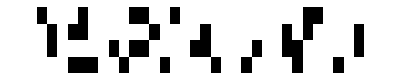
<|vr→-Graphics-,ggl→-Graphics-,bggl→-Graphics-|>

```mathematica
ClearAll[gglInit,bgglFromVRs, bgglFromGGL,toGGL];
Assert[Quotient[NSECTIONS,4]===4];
bgglFromVRs[mask_,vrs_List]:=
bgglFromGGL[toGGL[mask,vrs]];
bgglFromGGL[ggl_]:=Module[{group,result=zeroVR[],i,j},
For[i=0,i<NSECTIONS,i++,
For[j=0,j<NPLATS,j++,
group=Quotient[i,4];
result⟦i+1,j+1⟧=ggl⟦group+1,j+1⟧
]];result];
gglInit[]:=ConstantArray[1,{4,NPLATS}];
toGGL[mask_,vrs_List]:=
Module[{vr,ggl=gglInit[],bns=bitNumbersFromMask[mask]},
Assert[0≤Length[vrs]≤3,"incorrectNumberOfVRs"];
vr=oneVR[];
vr=Fold[andVRs[mask,#1,#2]&,vr,vrs];
Module[{i,line},
For[i=0,i<4,i++,
For[line=0, line<4, line++,
(* Stride is 4. *)
With[{index=4i+line},
If[MemberQ[bns,index],
ggl⟦i+1⟧=andWordlines[ggl⟦i+1⟧,vr⟦index+1⟧]
]]]]];ggl];
If[unitTesting,
Module[{v=randomizedVR[],ggl,bggl},
ggl=toGGL[16^^3333,{v}];
(* Always remember to add one to zero-based indices in Mathematica. *)
(* Here (and very often below), we do it explicitly in the brackets. *)
Assert[ggl⟦1+0⟧===andWordlines[v⟦1+0⟧,v⟦1+1⟧]];
bggl=bgglFromGGL[ggl];
echo@(tinyPlot/@<|"vr"->v,"ggl"->ggl,"bggl"->bggl|>);]]
```

### Instructions 1 through 3

The first three instructions (bundles of parallel commands enclosed in curly braces) put x⊻y (x XOR y) into RL and then some sections of RL into GGL.

1.1 	FFFF 	:	RL = SB[x];
}{ 2.1	FFFF 	:	RL ^= SB[y];
   2.2 	3333 	:	GGL = RL;
}{ 3.1	FFFF 	:	SB[x⊻y] = RL;

The section mask 16^^3333 is equivalent to the list of bit-numbers, {0, 1, 4, 5, 8, 9, C, D} (in hex). GGL has four rows (wordlines), corresponding to rows of a VR with mutually equal quotients to 4. Such rows are called groups. Thus, row 0 of GGL corresponds to rows 0, 1, 2, 3 of a VR, row 1 of GGL corresponds to rows 4, 5, 6, 7 of a VR, and so forth. Assignment to GGL from a VR automatically aggregates masked rows in a group via AND, hence our interpretation of command 2.2.

Let us write bit-number indices as subscripts in hex without commas to save space. c_("159D") means c_{1,5,9,D=13} and not c_("0x159D").

Also to save space and to make patterns of section indices more evident, write (x^y) as  x▴y, bound more tightly than & or |. It is Plus, without carry, in GF(2), the field of Booleans. We might write it as x⊻y, but that's longer and visually noisier.

It is already natural to write (x&y) as xy. We could write it as xy, but that's longer and crowds the indices. The point of shorter notation is to highlight the indices.

1.1:	RL_*:=x_*
2.1:	RL_*^=y_*
2.2:	GGL_("0123"):= (x▴y)_("048C")& (x▴y)_("159D")

3.1: Until RL is changed below, we know that RL==(x^y)==x▴y, all sections

26255

1500

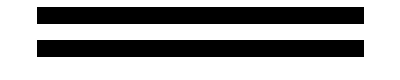
<|RL→-Graphics-,GGL→-Graphics-,bggl→-Graphics-,xy→-Graphics-,x▴y→-Graphics-|>

```mathematica
ClearAll[i1thru3];
i1thru3[bankA_Association,x_,y_]:=
Module[{
h=bankA,
xvr=vrFromImmediate[x],yvr=vrFromImmediate[y],xXORyVR},
xXORyVR=xorVRs[xvr,yvr]; (*instr 3*)
(*h["x"]=x;h["y"]=y;*)
h["RL"]=xXORyVR;
h["GGL"]=toGGL[16^^3333,{xXORyVR}];
h["bggl"]=bgglFromGGL[h["GGL"]];
h["xy"]=andVRs[xvr,yvr];
h["x▴y"]=xXORyVR;
h];
If[unitTesting,
echo[tinyPlot/@(globalBankUT=i1thru3[<||>,
echo@RandomInteger[{0,65535}],echo@RandomInteger[{0,65535}]])];
Assert[globalBankUT["GGL"]⟦1+0⟧===andWordlines[globalBankUT["x▴y"]⟦1+0⟧,globalBankUT["x▴y"]⟦1+1⟧]]]
```

### Instruction 4

}{ 4.1	1111	:	SB[cout1] = RL;
   4.2	1111<<1	:	SB[cout1] = GGL;
   4.3	1111<<2	:	RL = SB[x⊻y] & GGL;		/* (CIN & x⊻y) */
   4.4	3333	:	RL = SB[x,y];			/* CALC COUT0  */

Section mask 16^^1111 corresponds to hex bit numbers {0, 4, 8, C}=048C, 
16^^1111 << 1 to 16^^2222={1, 5, 9, D}=159D, 
16^^1111 << 2 to 16^^4444={2, 6, A, E}=26AE, and 
16^^1111 << 3 to 16^^8888={3, 7, B, F}=37BF.

When GGL appears on the right-hand side of an assignment, its four rows are broadcast to the masked destinations.

Multiple VRs (up to 3), comma-separated in an SB expression, as in SB[x,y], are implicitly ANDed.

Expressions with RL on the left-hand side are NOT proposed BELEX. They are merely for tracking the algorithm through the rest of this analysis. In our analysis, we always eliminate RL, by substitution, from the right-hand sides of expressions.

Letting c stand for cout1:
4.1:	c_("048C"):=(x▴y)_("048C")						subst RL from 2.1
4.2:	c_("159D"):=(x▴y)_("048C")&(x▴y)_("159D"), 				subst GGL from 2.2; implicit AND
4.3:	RL_("26AE"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")	subst GGL from 2.2; commute
4.4:	RL_("014589CD"):=xy_("014589CD")					SB[x,y]=x&y=xy

```mathematica
ClearAll[i4];
i4[bankA_Association]:=Module[{h=bankA},
(*4.1*)h["c"]=copyVR[16^^1111,h["x▴y"]];
Assert[h["c"]⟦1+0⟧===h["x▴y"]⟦1+0⟧];
Assert[h["c"]⟦1+4⟧===h["x▴y"]⟦1+4⟧];Assert[h["c"]⟦1+8⟧===h["x▴y"]⟦1+8⟧];
Assert[h["c"]⟦1+12⟧===h["x▴y"]⟦1+12⟧];
(*4.2*)h["c"]=copyVRsL[16^^2222,h["c"],h["bggl"]];
Assert[h["c"]⟦1+1⟧===andWordlines[h["x▴y"]⟦1+0⟧,h["x▴y"]⟦1+1⟧]];
Assert[h["c"]⟦1+5⟧===andWordlines[h["x▴y"]⟦1+4⟧,h["x▴y"]⟦1+5⟧]];
Assert[h["c"]⟦1+9⟧===andWordlines[h["x▴y"]⟦1+8⟧,h["x▴y"]⟦1+9⟧]];
Assert[h["c"]⟦1+13⟧===andWordlines[h["x▴y"]⟦1+12⟧,h["x▴y"]⟦1+13⟧]];
(*4.3*)h["rl"]=andVRsL[16^^4444,h["x▴y"],h["bggl"]];
echo[tinyPlot/@<|"x▴y"->h["x▴y"],"bggl"->h["bggl"],"and2"->andVRsL[16^^4444,h["x▴y"],h["bggl"]]|>];
(* bggl has the expected data in 26AE. *)
Assert[h["bggl"]⟦1+2⟧===
andWordlines[h["x▴y"]⟦1+0⟧,h["x▴y"]⟦1+1⟧]];
Assert[h["bggl"]⟦1+6⟧===
andWordlines[h["x▴y"]⟦1+4⟧,h["x▴y"]⟦1+5⟧]];
Assert[h["bggl"]⟦1+10⟧===andWordlines[h["x▴y"]⟦1+8⟧,h["x▴y"]⟦1+9⟧]];
Assert[h["bggl"]⟦1+14⟧===andWordlines[h["x▴y"]⟦1+12⟧,h["x▴y"]⟦1+13⟧]];
(* The expected wordlines are copied into RL. *)
Assert[h["rl"]⟦1+2⟧===
andWordlines[h["bggl"]⟦1+2⟧,h["x▴y"]⟦1+2⟧]];
Assert[h["rl"]⟦1+6⟧===
andWordlines[h["bggl"]⟦1+6⟧,h["x▴y"]⟦1+6⟧]];
Assert[h["rl"]⟦1+10⟧===
andWordlines[h["bggl"]⟦1+10⟧,h["x▴y"]⟦1+10⟧]];
Assert[h["rl"]⟦1+14⟧===
andWordlines[h["bggl"]⟦1+14⟧,h["x▴y"]⟦1+14⟧]];
(* The substitution for bggl is correct. *)
Assert[h["rl"]⟦1+2⟧===
andWordlines[
andWordlines[h["x▴y"]⟦1+0⟧,h["x▴y"]⟦1+1⟧],
h["x▴y"]⟦1+2⟧]];
Assert[h["rl"]⟦1+6⟧===
andWordlines[
andWordlines[h["x▴y"]⟦1+4⟧,h["x▴y"]⟦1+5⟧],
h["x▴y"]⟦1+6⟧]];
Assert[h["rl"]⟦1+10⟧===
andWordlines[
andWordlines[h["x▴y"]⟦1+8⟧,h["x▴y"]⟦1+9⟧],
h["x▴y"]⟦1+10⟧]];
Assert[h["rl"]⟦1+14⟧===
andWordlines[
andWordlines[h["x▴y"]⟦1+12⟧,h["x▴y"]⟦1+13⟧],
h["x▴y"]⟦1+14⟧]];
(*4.4*)
h]
If[unitTesting,echo[tinyPlot/@i4[globalBankUT]];]
```

<|x▴y→-Graphics-,bggl→-Graphics-,and2→-Graphics-|>

<|RL→-Graphics-,GGL→-Graphics-,bggl→-Graphics-,xy→-Graphics-,x▴y→-Graphics-,c→-Graphics-,rl→-Graphics-|>

### Instruction 5

}{ 5.1	1111<<2	:	SB[cout1] = RL;
   5.2	1111<<3	:	RL = SB[x⊻y] & NRL;		/* (CIN & x⊻y) */
   5.3	1111<<1	:	RL |= SB[x⊻y] & NRL;	/* (CIN & x⊻y) */
   5.4	1111<<2	:	RL = SB[x,y];			/* CALC COUT0 */

NRL semantics (example): NRL_("37BF")=RL_("26AE"). Just subtract 1 from each of NRL’s section bit-numbers and substitute RL for NRL.

5.1:	c_("26AE"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")			RL from 4.3
5.2:	RL_("37BF"):=(x▴y)_("37BF")&NRL_("37BF")
	RL_("37BF"):=(x▴y)_("37BF")&RL_("26AE")					NRL semantics
	RL_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")
											RL from 4.3; commute
5.3:	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&NRL_("159D"))
	RL_("159D"):=RL_("159D")|((x▴y)_("159D")&RL_("048C"))		NRL semantics
	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&RL_("048C"))		RL_("159D") from 4.4
	RL_("159D"):=xy_("159D")|((x▴y)_("159D")&xy_("048C"))			RL_("048C") from 4.4
	RL_("159D"):=(xy_("159D")|(x▴y)_("159D"))&(xy_("159D")|xy_("048C"))	distrib to CNF
5.4	RL_("26AE"):=xy_("26AE")

All “reads” into RL are compatible because their section masks are disjoint.

### Instruction 6

}{ 6.1	1111<<3	:	SB[cout1] = RL;
   6.2	1111<<3	:	RL = SB[x,y];
   6.3	1111<<2	:	RL |= SB[x⊻y] & NRL;	/* (CIN & x⊻y) = COUT? */
   6.4	0001	:	GGL = RL;

6.1:	c_("37BF"):=RL_("37BF")
	c_("37BF"):=(x▴y)_("048C")&(x▴y)_("159D")&(x▴y)_("26AE")&(x▴y)_("37BF")		RL_("37BF") from 5.2
6.2:	RL_("37BF"):=xy_("37BF")		Section 9.1: safe write (6.1) before read RL_("37BF") (6.2)
6.3:	RL_("26AE"):=RL_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))
	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&NRL_("26AE"))				from 5.4
	RL_("26AE"):=xy_("26AE")|((x▴y)_("26AE")&RL_("159D"))				NRL semantics
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))&(xy_("26AE")|RL_("159D"))		distrib
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))
&(xy_("26AE")|((xy_("159D")|(x▴y)_("159D"))&(xy_("159D")|xy_("048C"))))	RL_("159D") from 5.3	
	RL_("26AE"):=(xy_("26AE")|(x▴y)_("26AE"))
&(xy_("26AE")|xy_("159D")|(x▴y)_("159D"))
&(xy_("26AE")|xy_("159D")|xy_("048C"))						distrib		
6.4	GGL_0:=RL_0
	GGL_0:=xy_0										from 4.4
	GGL_123=(x▴y)_("48C")&(x▴y)_("59D")							from 2.2 (unchanged)

Notice symmetry between 5.3 and 6.3.

### Instruction 7

}{ 7.1	1111<<3	:	RL |= SB[x⊻y] & NRL;	/* (CIN & x⊻y) */
   7.2	0001<<3	:	GL = RL;
   7.3	0001	:	RL = SB[cout1];

7.1:	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&NRL_("37BF"))
	RL_("37BF"):=RL_("37BF")|((x▴y)_("37BF")&RL_("26AE"))				NRL semantics
	RL_("37BF"):=xy_("37BF")|((x▴y)_("37BF")&RL_("26AE"))					from 6.2
	RL_("37BF"):=xy_("37BF")|(x▴y)_("37BF")&RL_("26AE")

```mathematica
ClearAll[instrs1and2];
instrs1and2[bankAssoc_,x_,y_]:=
Module[{bank=bankAssoc},
bank["RL"]=xorVRs[x,y];
bank];
```

<|RL→{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}|>

}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\

}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\

}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\

}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\

}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\

}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\

}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\

}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\

}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\

}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

## Section Appendix: Formal Spot-Checking

Spot-check the definition of Var(k) at the edges of the piecewise formula.

```mathematica
ClearAll[var];

With[{V=24,P=2048,S=16,G=4,R=128},
var[k1_]:=With[{k=k1-1},
Piecewise[{{MMB[Mod[Quotient[k,P S],V],
Mod[Quotient[k,S],P],
Mod[k,S]], 0≤k<V P S}, {With[{kp=k-V P S},
RL[Mod[Quotient[kp,S],P],
Mod[kp,S]]], V P S≤k<V P S+P S}, {With[{kpp=k-V P S-P S},
GL[Mod[kpp,P]]], V P S+P S≤k<V P S+P S+P}, {With[{kppp=k-V P S-P S-P},
GGL[Mod[Quotient[kppp,G],P],
Mod[kppp,G]]], V P S+P S+P≤k<V P S+P S+P+P G}, {With[{kpppp=k-V P S-P S-P-P G},
RSP16[Mod[Quotient[kpppp,S],R],
Mod[kpppp,S]]], V P S+P S+P+P G≤k<V P S+P S+P+P G+R S}, {Throw["Index out of range"], True}}]]]
```

```mathematica
var[0]
```

Throw::nocatch: Uncaught Throw[Index out of range] returned to top level.

Hold[Throw[Index out of range]]

```mathematica
var[1]
```

MMB[0,0,0]

```mathematica
var[2]
```

MMB[0,0,1]

```mathematica
var[17]
```

MMB[0,1,0]

```mathematica
var[786432]
```

MMB[23,2047,15]

```mathematica
var[786432+1]
```

RL[0,0]

```mathematica
var[786432+32768]
```

RL[2047,15]

```mathematica
var[786432+32768+1]
```

GL[0]

```mathematica
var[786432+32768+2048]
```

GL[2047]

```mathematica
var[786432+32768+2048+1]
```

GGL[0,0]

```mathematica
var[786432+32768+2048+8192]
```

GGL[2047,3]

```mathematica
var[786432+32768+2048+8192+1]
```

RSP16[0,0]

```mathematica
var[786432+32768+2048+8192+2048]
```

RSP16[127,15]

```mathematica
var[831489]
```

Throw::nocatch: Uncaught Throw[Index out of range] returned to top level.

Hold[Throw[Index out of range]]

```mathematica
/*
 * Copyright (C) 2020, GSI Technology, Inc. All rights reserved.
 *
 * This software source code is the sole property of GSI Technology, Inc.
 * and is proprietary and confidential.
 */

#ifndef ARITH_INST_APL_H
#define ARITH_INST_APL_H

#include <add_sub_utils.apl.h>
#include <common_defs.apl.h>

// *INDENT-OFF*

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/
#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		 SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_FLAG_CICO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		(SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];					\
		(SM_0X0001 << C_FLAG):	GL = RL;						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL = SB[x];						\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;		/* Dummy use of GL */	\
	}{ /* 3 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 4 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 5 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 6 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 8 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 9 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 10 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 12 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 13 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 14 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;


#define ARITH_ADD_S16_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<14):	GGL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001<<15):	RL ^= NRL;						\
		(SM_0X0001<<15):	GL = RL;						\
		~(SM_0X0001<<15):	RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
	}{ /* 13 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_ABS_U16_S16_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;						\
	}{ /* 13 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;

#define ARITH_SUB_ABS_U16_S16_T0_INST(x, y, res, x_xor_noty, cout1, noty)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = ~SB[y] & INV_RSP16;				\
	}{ /* 2 */										\
		SM_0XFFFF:		SB[noty] = RL;						\
		SM_0XFFFF:		RL ^= SB[x]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_noty] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_noty] & GGL;	/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,noty];		/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,noty];		/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,noty];		/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		SM_0X000F:		RL |= SB[cout1];					\
		(SM_0X0001<<3):		GL = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_noty] ^ NRL;				\
		SM_0X0001:		RL = ~SB[x_xor_noty] & INV_RSP16;			\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;						\
	}{ /* 14 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_noty] ^ GGL;				\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;


#define ARITH_ADD_S16_CIN_T0_INST(x, y, t_xory_cbi_t0, t_cbi0, t_cbi1, res) \
                (SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];	/* Load carry in */ \
		(SM_0X0001 << C_FLAG):	GL = RL;		/* Set GL with carry in */ \
	}{ \
		SM_0X0001:	RL = SB[x] & GL;		/* RL[0] = x&ci */ \
		SM_0X0001:	SB[t_xory_cbi_t0] = GL;	/* Save Carry-In in t_xory_cbi_t0 */ \
		~SM_0X0001:	RL = SB[x];		/* RL[1-15] = x */ \
	}{ \
		SM_0X0001:	RL |= SB[y, t_xory_cbi_t0];	/* RL[0] = y&ci | x&ci */ \
		~SM_0X0001:	RL |= SB[y];		/* RL[1-15] = x|y */ \
	}{ \
		~SM_0X0001:	SB[t_xory_cbi_t0] = RL;	/* t_xory_cbi_t0[1-15] = x|y */ \
		~SM_0X0001:	RL = SB[x , y];		/* RL[1-15] = x&y */ \
		SM_0X0001:	RL |= SB[x , y];		/* RL[0]= Cout = x&y | y&ci | x&ci */ \
	}{ \
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;	/* t_cbi0[5,9,13] = x&y */ \
		(SM_0X1111 << 1):	RL |= SB[t_xory_cbi_t0] & NRL; /* RL[1] = Cout[1] = x&y | ci(x|y) */ \
							               /* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */ \
		(SM_0X1111 << 4):	RL |= SB[t_xory_cbi_t0];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */ \
	}{ \
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 2):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 5):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
	}{ \
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 3):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 6):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		(SM_0X1111 << 7):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */ \
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */ \
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */ \
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */ \
	}{ \
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */ \
	}{ \
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */ \
	}{ \
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL; \
		SM_0X0001:	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	RL ^= GL; \
		SM_0X0001:	GL = RL; \
	}{ \
		SM_0X0001:	RL = SB[t_xory_cbi_t0]; \
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL; \
	}{ \
		SM_0XFFFF:	RL ^= SB[x]; \
	}{ \
		SM_0XFFFF:	RL ^= SB[y]; \
	}{ \
		SM_0XFFFF:	SB[res] = RL;	/* res = Cin^x^y */

#define ARITH_SUB_U16_T3_INST(x, y, res) \
                SM_0X0001:	SB[RN_REG_T0] = RSP16; \
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */      \
	}{ \
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */  \
	}{ \
		~SM_0X0001:	SB[RN_REG_T0] = INV_RL;        \
		SM_0X0001:	SB[RN_REG_T1] = INV_RL;    \
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */	 \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res) \


#define ARITH_SUB_U16_NO_BOUT_T0_INST(x, y, res, t_notxxory, t_cbi0, t_cbi1)					\
	   /* 1 */												\
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */					\
	}{ /* 2 */												\
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */					\
	}{ /* 3 */												\
		SM_0XFFFF:	SB[t_notxxory] = INV_RL;							\
		SM_0X0001:	SB[t_cbi0] = INV_RL;								\
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */						\
	}{ /* 4 */												\
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;		/* t_cbi0[5,9,13] = x&y */		\
		(SM_0X1111 << 1):	RL |= SB[t_notxxory] & NRL;	/* RL[1] = Cout[1] = x&y | ci(x|y) */	\
							/* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */	\
		(SM_0X1111 << 4):	RL |= SB[t_notxxory];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */\
	}{ /* 5 */												\
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 2):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 5):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
	}{ /* 6 */												\
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 3):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 6):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 7 */												\
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		(SM_0X1111 << 7):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 8 */												\
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */			\
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */			\
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */			\
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */			\
	}{ /* 9 */												\
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */			\
	}{ /* 10 */												\
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */			\
	}{ /* 11 */												\
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL;							\
		SM_0X0001:		RL = RSP16;								\
	}{ /* 12 */												\
		SM_0XFFFF:	RL ^= SB[t_notxxory];								\
	}{ /* 13 */												\
		SM_0XFFFF:	SB[res] = INV_RL;	/* res = Cin^x^y */

#define ARITH_SUB_S16_T3_INST(res, x, y) \
                        SM_0X0001:	SB[RN_REG_T0] = RSP16; \
                        SM_0XFFFF:	RL = SB[x]; \
                }{ \
                        SM_0XFFFF:	RL ^= SB[y]; \
                }{ \
                        ~SM_0X0001:	SB[RN_REG_T0] = INV_RL; \
                        SM_0X0001:	SB[RN_REG_T1] = INV_RL; \
                        SM_0XFFFF:	RL &= SB[y]; \
                }{ \
                        PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                        KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
                }{ \
                        SUM_SUB_INST(x, y, res)

#define ARITH_SUB_U16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
	}{ \
                SUM_SUB_INST(x, y, res)

#define ARITH_SUB_S16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res)

// input: x, y
// output:	s0 = y[0] ? x>>1 : 0
//		_2x = rotate_left(x)
//		m0 = y[2] ? 0xffff : 0
//		t_y_res_lsb[0]     = y[0] & x[0]
//			   [15..1] = y[15..1]
//		RL = y[1] ? x : 0
#define ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)			\
		SM_0XFFFF:	RL = SB[y];							\
	}{											\
		SM_0XFFFF:	SB[t_y_res_lsb] = RL;	/*t_y_res_lsb = y */			\
		(SM_0X0001 << 2):	GL = RL;	/*GL = y[2]	  */			\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;	/* m0 = y[2] ? 0xffff : 0 */		\
		SM_0XFFFF:		RL = SB[x];	/* RL = x */				\
		(SM_0X0001 << 15):	GGL = RL;	/* GL = x[15] */			\
	}{											\
		~SM_0X0001:	SB[_2x] = NRL;		/* _2x = rotate_left(x) */		\
		SM_0X0001:	RL = SB[t_y_res_lsb];						\
		SM_0X0001:	GL = RL;		/* GL = t_y_res_lsb[0] (= y[0]) */	\
		SM_0X0001:	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[0] ? x ; 0 */			\
	}{											\
		SM_0X0001:	SB[t_y_res_lsb] = RL;	/* t_y_res_lsb[0] = y[0] & x[0]; */	\
		(SM_0X0001 << 15):	SB[s0, s1] = GGL;					\
		(SM_0X00FF << 1):	SB[m1] = RSP16;							\
		(SM_0X00FF << 7):	SB[m1] = RSP16;							\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;	/* s0[15..0] = y[0] ? x>>1 : 0 */	\
		(SM_0X0001 << 1):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 1):	GL = RL;	/* GL[1] = t_y_res_lsb[1] (= y[1]) */	\
		(SM_0X0001 << 15):	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[1] ? x : 0 */			\

#define ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 3):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 3):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 1):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 4):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 4):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 2):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{ 											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 5):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 5):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{ 											\
		(SM_0X0001 << 3):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 6):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 6):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 4):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 7):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 7):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{	(SM_0X0001 << 5):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 8):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 8):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 6):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 9):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 9):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 7):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 10):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 10):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 8):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}											\
	{	~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 11):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 11):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 9):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 12):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 12):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{	SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 10):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 13):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 13):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 11):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 14):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 14):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 12):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m0];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
		(SM_0X0001 << 15):	GGL = RL;						\
	}{											\
		(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	GL = RL;						\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 13):	SB[t_y_res_lsb] = GL; 					\
		SM_0X0001:		RL = SB[c, s0];						\
		(sm_0x3fff << 1):	RL |= SB[_2x, m0, c_xor_s];				\
		(SM_0X0001 << 15):	RL = SB[_2x, m0, c_xor_s] | GGL;			\

#define ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m1];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
	}{											\
		(SM_0X0001 << 14):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define	ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)					\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	RL = SB[s0, m1];					\
	}{ /* 1 */										\
		~(SM_0X0001 << 15):	SB[res_lsb] = RL;					\
		(SM_0X0001 << 15):	SB[s0] = RL;						\
		SM_0XFFFF:		RL = SB[c];						\
	}											\

#define ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)			\
	{/* 2 */										\
		SM_0XFFFF:		RL ^= SB[s0]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[s1] = RL;						\
	}{ /* 4 */										\
		SM_0X1111:		SB[_2x] = RL;						\
		(SM_0X1111<<1):		SB[_2x] = GGL;						\
		(SM_0X1111<<2):		RL = SB[s1] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[c,s0];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[c,s0];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[c,s0];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[_2x];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res_msb] = RL;					\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[_2x] & GL;					\
	}{ /* 11 */										\
		(SM_0X0001 << 15):	SB[res_msb] = RL;					\
	}{	/* end_mul_16() */								\
		~SM_0X0001:		RL = SB[s1] ^ NRL;					\
		SM_0X0001:		RL = SB[res_msb];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		~(SM_0X0001 << 15):	SB[res_msb] = SRL;					\
		(SM_0X0001 << 15):	SB[res_lsb] = GL;					\

#define ARITH_MUL_U16_T0_INST(res_lsb, res_msb, x, y,						\
			      c_xor_s,								\
			      s0, s1, _2x, 							\
			      m0, m1, t_y_res_lsb,						\
			      c,								\
			      sm_0x3fff)							\
		ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{											\
		ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)				\
		ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)		\

// *INDENT-ON*

#endif /* ARITH_INST_APL_H */
```

```mathematica
/*
 * Copyright (C) 2020, GSI Technology, Inc. All rights reserved.
 *
 * This software source code is the sole property of GSI Technology, Inc.
 * and is proprietary and confidential.
 */

#ifndef ARITH_INST_APL_H
#define ARITH_INST_APL_H

#include <add_sub_utils.apl.h>
#include <common_defs.apl.h>

// *INDENT-OFF*

/*
 * addsub_frag_add_u16(RN_REG x, RN_REG y, RN_REG res, RN_REG x_xor_y, RN_REG cout1)
 * cout1[0] = X[0]^Y[0];
 * cout1[1] = (X[0]^Y[0]) & (X[1]^Y[1]);
 * cout1[2] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]);
 * cout1[3] = (X[0]^Y[0]) & (X[1]^Y[1]) & (X[2]^Y[2]) & (X[3]^Y[3]);
 * cout0[0] = X[0]&Y[0];
 * cout0[1] = X[1]&Y[1] | (COUT0[0] & X[1]^Y[1]);
 * cout0[2] = X[2]&Y[2] | (COUT0[1] & X[2]^Y[2]);
 * cout0[3] = X[3]&Y[3] | (COUT0[2] & X[3]^Y[3]);
*/
#define ARITH_ADD_U16_GL_CO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		 SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CICO_FLAG_CO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 4 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_FLAG_CICO_T0_INST(x, y, res, x_xor_y, cout1)			\
	   /* 1 */										\
		(SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];					\
		(SM_0X0001 << C_FLAG):	GL = RL;						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL = SB[x];						\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;		/* Dummy use of GL */	\
	}{ /* 3 */										\
		SM_0X0001:		SB[x_xor_y] = GL;					\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 4 */										\
		~SM_0X0001:		SB[x_xor_y] = RL;					\
		SM_0X0001:		RL ^= SB[x_xor_y];		/* Calc bit-0 res */	\
		SM_0X1111:		SB[cout1] = RL;						\
	}{ /* 5 */										\
		SM_0X0001:		SB[x_xor_y] = RL;		/* Keep bit-0 res */	\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 6 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		/*SM_0X0001:		GGL = RL;*/						\
	}{ /* 8 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 9 */										\
		(SM_0X000F<<0):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<3):		GL = RL;						\
		/*SM_0X0001:		RL = SB[cout1];	*/					\
	}{ /* 10 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		/*SM_0X0001:		SB[res] = RL;*/						\
	}{ /* 11 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		/*SM_0X0001:		RL = GGL;*/						\
	}{ /* 12 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 13 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		 SM_0X0001:		RL = SB[x_xor_y];		/* Restore bit-0 res */	\
		(SM_0X0001 << C_FLAG):	SB[RN_REG_FLAGS] = GL;					\
	}{ /* 14 */										\
		SM_0XFFFF:		SB[res] = RL;

#define ARITH_ADD_U16_GL_CO_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
		SM_0X0001:		SB[cout1] = GL;			/* Dummy use of GL */	\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;


#define ARITH_ADD_S16_T0_INST(x, y, res, x_xor_y, cout1)					\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<14):	GGL = RL;						\
	}{ /* 11 */										\
		(SM_0X0001<<15):	RL ^= NRL;						\
		(SM_0X0001<<15):	GL = RL;						\
		~(SM_0X0001<<15):	RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL;					\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
	}{ /* 13 */										\
		~SM_0X0001:		SB[res] = RL;

#define ARITH_ADD_ABS_U16_S16_T0_INST(x, y, res, x_xor_y, cout1)				\
	   /* 1 */										\
		SM_0XFFFF:		RL = SB[x];						\
	}{ /* 2 */										\
		SM_0XFFFF:		RL ^= SB[y]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_y] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_y] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,y];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_y] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,y];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,y];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_y] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[cout1];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res] = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 11 */										\
		~SM_0X0001:		RL = SB[x_xor_y] ^ NRL;					\
	}{ /* 12 */										\
		~SM_0X0001:		SB[res] = RL;						\
	}{ /* 13 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_y] ^ GGL;					\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;

#define ARITH_SUB_ABS_U16_S16_T0_INST(x, y, res, x_xor_noty, cout1, noty)			\
	   /* 1 */										\
		SM_0XFFFF:		RL = ~SB[y] & INV_RSP16;				\
	}{ /* 2 */										\
		SM_0XFFFF:		SB[noty] = RL;						\
		SM_0XFFFF:		RL ^= SB[x]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[x_xor_noty] = RL;					\
	}{ /* 4 */										\
		SM_0X1111:		SB[cout1] = RL;						\
		(SM_0X1111<<1):		SB[cout1] = GGL;					\
		(SM_0X1111<<2):		RL = SB[x_xor_noty] & GGL;	/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[x,noty];		/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[x,noty];		/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[cout1] = RL;						\
		(SM_0X1111<<3):		RL = SB[x,noty];		/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[x_xor_noty] & NRL;	/* (CIN & xXORy) */	\
	}{ /* 8 */										\
		SM_0X000F:		RL |= SB[cout1];					\
		(SM_0X0001<<3):		GL = RL;						\
	}{ /* 9 */										\
		(SM_0X000F<<4):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
	}{ /* 10 */										\
		(SM_0X000F<<8):		RL |= SB[cout1] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
	}{ /* 11 */										\
		(SM_0X000F<<12):	RL |= SB[cout1] & GL;					\
		(SM_0X0001<<15):	GGL = RL;						\
	}{ /* 12 */										\
		~SM_0X0001:		RL = SB[x_xor_noty] ^ NRL;				\
		SM_0X0001:		RL = ~SB[x_xor_noty] & INV_RSP16;			\
	}{ /* 13 */										\
		SM_0XFFFF:		SB[res] = RL;						\
	}{ /* 14 */										\
		(SM_0X0001<<15):	RL = SB[x_xor_noty] ^ GGL;				\
		(SM_0X0001<<15):	GL = RL;						\
	}											\
	apl_if_gl_negate_t1(res)								\
	{											\
		SM_0XFFFF:      SB[res] = RL;


#define ARITH_ADD_S16_CIN_T0_INST(x, y, t_xory_cbi_t0, t_cbi0, t_cbi1, res) \
                (SM_0X0001 << C_FLAG):	RL = SB[RN_REG_FLAGS];	/* Load carry in */ \
		(SM_0X0001 << C_FLAG):	GL = RL;		/* Set GL with carry in */ \
	}{ \
		SM_0X0001:	RL = SB[x] & GL;		/* RL[0] = x&ci */ \
		SM_0X0001:	SB[t_xory_cbi_t0] = GL;	/* Save Carry-In in t_xory_cbi_t0 */ \
		~SM_0X0001:	RL = SB[x];		/* RL[1-15] = x */ \
	}{ \
		SM_0X0001:	RL |= SB[y, t_xory_cbi_t0];	/* RL[0] = y&ci | x&ci */ \
		~SM_0X0001:	RL |= SB[y];		/* RL[1-15] = x|y */ \
	}{ \
		~SM_0X0001:	SB[t_xory_cbi_t0] = RL;	/* t_xory_cbi_t0[1-15] = x|y */ \
		~SM_0X0001:	RL = SB[x , y];		/* RL[1-15] = x&y */ \
		SM_0X0001:	RL |= SB[x , y];		/* RL[0]= Cout = x&y | y&ci | x&ci */ \
	}{ \
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;	/* t_cbi0[5,9,13] = x&y */ \
		(SM_0X1111 << 1):	RL |= SB[t_xory_cbi_t0] & NRL; /* RL[1] = Cout[1] = x&y | ci(x|y) */ \
							               /* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */ \
		(SM_0X1111 << 4):	RL |= SB[t_xory_cbi_t0];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */ \
	}{ \
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 2):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 5):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
	}{ \
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */ \
		(SM_0X1111 << 3):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout0 */ \
		(SM_0X1111 << 6):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */ \
		(SM_0X1111 << 7):	RL |= SB[t_xory_cbi_t0] & NRL;	/* Propagate Cout1 */ \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */ \
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */ \
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */ \
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */ \
	}{ \
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */ \
	}{ \
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */ \
	}{ \
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL; \
		SM_0X0001:	RL |= SB[t_cbi1] & GL; \
		(SM_0X0001 << 15):	GL = RL; \
	}{ \
		SM_0X0001:	RL ^= GL; \
		SM_0X0001:	GL = RL; \
	}{ \
		SM_0X0001:	RL = SB[t_xory_cbi_t0]; \
		(SM_0X0001 << OF_FLAG):	SB[RN_REG_FLAGS] = GL; \
	}{ \
		SM_0XFFFF:	RL ^= SB[x]; \
	}{ \
		SM_0XFFFF:	RL ^= SB[y]; \
	}{ \
		SM_0XFFFF:	SB[res] = RL;	/* res = Cin^x^y */

#define ARITH_SUB_U16_T3_INST(x, y, res) \
                SM_0X0001:	SB[RN_REG_T0] = RSP16; \
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */      \
	}{ \
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */  \
	}{ \
		~SM_0X0001:	SB[RN_REG_T0] = INV_RL;        \
		SM_0X0001:	SB[RN_REG_T1] = INV_RL;    \
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */	 \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res) \


#define ARITH_SUB_U16_NO_BOUT_T0_INST(x, y, res, t_notxxory, t_cbi0, t_cbi1)					\
	   /* 1 */												\
		SM_0XFFFF:	RL = SB[x];		/* RL[0-15] = x */					\
	}{ /* 2 */												\
		SM_0XFFFF:	RL ^= SB[y];		/* RL[0-15] = x ^ y */					\
	}{ /* 3 */												\
		SM_0XFFFF:	SB[t_notxxory] = INV_RL;							\
		SM_0X0001:	SB[t_cbi0] = INV_RL;								\
		SM_0XFFFF:	RL &= SB[y];		/* RL = x */						\
	}{ /* 4 */												\
		(SM_0X1111 << 1):	SB[t_cbi0] = NRL;		/* t_cbi0[5,9,13] = x&y */		\
		(SM_0X1111 << 1):	RL |= SB[t_notxxory] & NRL;	/* RL[1] = Cout[1] = x&y | ci(x|y) */	\
							/* 5,9,13:	RL = Cout0[5,9,13] = x&y | ci(x|y) */	\
		(SM_0X1111 << 4):	RL |= SB[t_notxxory];	/* RL[4,8,12] = Cout1[4,8,12] = x&y | 1&(x|y) */\
	}{ /* 5 */												\
		(SM_0X1111 << 2):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 2):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 5):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
	}{ /* 6 */												\
		(SM_0X1111 << 3):	SB[t_cbi0] = NRL;	/* Propagate Cin0 */				\
		(SM_0X1111 << 3):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout0 */			\
		(SM_0X1111 << 6):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 7 */												\
		(SM_0X1111 << 4):	SB[t_cbi0] = NRL;	/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		SM_0X0001:	SB[t_cbi0] = GL;		/* t_cbi0[8,12,16] = Cout0[7, 11, 15] */	\
		(SM_0X1111 << 7):	RL |= SB[t_notxxory] & NRL;	/* Propagate Cout1 */			\
		(SM_0X0001 << 15):	GL = RL;								\
	}{ /* 8 */												\
		SM_0X0001:	SB[t_cbi1] = GL;			/* save Cin1 pred */			\
		(SM_0XFFFF << 5):	SB[t_cbi1] = NRL;		/* save Cin1 pred */			\
		SM_0XFFFF:	RL = SB[t_cbi0];			/* Load Cin0 pred */			\
		(SM_0X0001 << 4):	GL = RL;			/* Calc Cin[4..7] */			\
	}{ /* 9 */												\
		(SM_0X000F << 5):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 8):	GL = RL;			/* Calc Cin[8..11] */			\
	}{ /* 10 */												\
		(SM_0X000F << 9):	RL |= SB[t_cbi1] & GL;							\
		(SM_0X0001 << 12):	GL = RL;			/* Calc Cin[12..15] */			\
	}{ /* 11 */												\
		(SM_0X000F << 13):	RL |= SB[t_cbi1] & GL;							\
		SM_0X0001:		RL = RSP16;								\
	}{ /* 12 */												\
		SM_0XFFFF:	RL ^= SB[t_notxxory];								\
	}{ /* 13 */												\
		SM_0XFFFF:	SB[res] = INV_RL;	/* res = Cin^x^y */

#define ARITH_SUB_S16_T3_INST(res, x, y) \
                        SM_0X0001:	SB[RN_REG_T0] = RSP16; \
                        SM_0XFFFF:	RL = SB[x]; \
                }{ \
                        SM_0XFFFF:	RL ^= SB[y]; \
                }{ \
                        ~SM_0X0001:	SB[RN_REG_T0] = INV_RL; \
                        SM_0X0001:	SB[RN_REG_T1] = INV_RL; \
                        SM_0XFFFF:	RL &= SB[y]; \
                }{ \
                        PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                        KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
                }{ \
                        SUM_SUB_INST(x, y, res)

#define ARITH_SUB_U16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_BO_LOAD_BI_INST(RN_REG_T0) \
	}{ \
                SUM_SUB_INST(x, y, res)

#define ARITH_SUB_S16_BIN_T3_INST(res, x, y) \
                (SM_0X0001 << B_FLAG):	RL = SB[RN_REG_FLAGS]; \
                (SM_0X0001 << B_FLAG):	GL = RL; \
        }{ \
                PROPAGATE_BORROW_BI_INIT(x, y, RN_REG_T0, RN_REG_T1) \
        }{ \
                PROPAGATE_CARRY_BORROW_3PRED_INST(x, y, RN_REG_T0, RN_REG_T1, RN_REG_T2) \
                KEEP_OF_LOAD_CBI_INST(RN_REG_T0) \
        }{ \
                SUM_SUB_INST(x, y, res)

// input: x, y
// output:	s0 = y[0] ? x>>1 : 0
//		_2x = rotate_left(x)
//		m0 = y[2] ? 0xffff : 0
//		t_y_res_lsb[0]     = y[0] & x[0]
//			   [15..1] = y[15..1]
//		RL = y[1] ? x : 0
#define ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)			\
		SM_0XFFFF:	RL = SB[y];							\
	}{											\
		SM_0XFFFF:	SB[t_y_res_lsb] = RL;	/*t_y_res_lsb = y */			\
		(SM_0X0001 << 2):	GL = RL;	/*GL = y[2]	  */			\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;	/* m0 = y[2] ? 0xffff : 0 */		\
		SM_0XFFFF:		RL = SB[x];	/* RL = x */				\
		(SM_0X0001 << 15):	GGL = RL;	/* GL = x[15] */			\
	}{											\
		~SM_0X0001:	SB[_2x] = NRL;		/* _2x = rotate_left(x) */		\
		SM_0X0001:	RL = SB[t_y_res_lsb];						\
		SM_0X0001:	GL = RL;		/* GL = t_y_res_lsb[0] (= y[0]) */	\
		SM_0X0001:	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[0] ? x ; 0 */			\
	}{											\
		SM_0X0001:	SB[t_y_res_lsb] = RL;	/* t_y_res_lsb[0] = y[0] & x[0]; */	\
		(SM_0X0001 << 15):	SB[s0, s1] = GGL;					\
		(SM_0X00FF << 1):	SB[m1] = RSP16;							\
		(SM_0X00FF << 7):	SB[m1] = RSP16;							\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;	/* s0[15..0] = y[0] ? x>>1 : 0 */	\
		(SM_0X0001 << 1):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 1):	GL = RL;	/* GL[1] = t_y_res_lsb[1] (= y[1]) */	\
		(SM_0X0001 << 15):	SB[m1] = RSP16;							\
	}{											\
		SM_0XFFFF:	RL = SB[x] & GL;	/* RL = y[1] ? x : 0 */			\

#define ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 3):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 3):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 1):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 4):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 4):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 2):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{ 											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 5):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 5):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{ 											\
		(SM_0X0001 << 3):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 6):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 6):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 4):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 7):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 7):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{	(SM_0X0001 << 5):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 8):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 8):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 6):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 9):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 9):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 7):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 10):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 10):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 8):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 					\
				  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}											\
	{	~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 11):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 11):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 9):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 12):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 12):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{	SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 10):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m0];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 13):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 13):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 11):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s0];						\
		~SM_0X0001:		RL |= SB[_2x, m0, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:	SB[c_xor_s] = RL;						\
		~SM_0X0001:	RL ^= SB[_2x, m1];						\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 14):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 14):	GL = RL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[m0] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 12):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s0];						\
		(SM_0X0001 << 15):	RL ^= SB[s0, m1];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m0];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s1] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s0, m1];					\
		(SM_0X0001 << 15):	GGL = RL;						\
	}{											\
		(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	GL = RL;						\
	}{											\
		SM_0XFFFF:		SB[m1] = GL;						\
		(sm_0x3fff << 1):	RL = SB[c, s0];						\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(SM_0X0001 << 13):	SB[t_y_res_lsb] = GL; 					\
		SM_0X0001:		RL = SB[c, s0];						\
		(sm_0x3fff << 1):	RL |= SB[_2x, m0, c_xor_s];				\
		(SM_0X0001 << 15):	RL = SB[_2x, m0, c_xor_s] | GGL;			\

#define ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 					\
				   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)			\
		SM_0XFFFF:		SB[c] = RL;						\
		~(SM_0X0001 << 15):	RL ^= SB[s1];						\
		(SM_0X0001 << 15):	RL ^= SB[s1, m0];					\
	}{											\
		SM_0XFFFF:		SB[c_xor_s] = RL;					\
		~SM_0X0001:		RL ^= SB[_2x, m1];					\
	}{											\
		~(SM_0X0001 << 15):	SB[s0] = SRL;						\
		(SM_0X0001 << 15):	RL = SB[c, s1, m0];					\
		SM_0X0001:		RL = SB[c_xor_s];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		(sm_0x3fff << 1):	RL = SB[c, s1];						\
	}{											\
		(SM_0X0001 << 14):	SB[t_y_res_lsb] = GL;					\
		SM_0X0001:		RL = SB[c, s1];						\
		~SM_0X0001:		RL |= SB[_2x, m1, c_xor_s];				\

#define	ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)					\
		SM_0XFFFF:	SB[c] = RL;							\
		~(SM_0X0001 << 15):	RL = SB[t_y_res_lsb];					\
		(SM_0X0001 << 15):	RL = SB[s0, m1];					\
	}{ /* 1 */										\
		~(SM_0X0001 << 15):	SB[res_lsb] = RL;					\
		(SM_0X0001 << 15):	SB[s0] = RL;						\
		SM_0XFFFF:		RL = SB[c];						\
	}											\

#define ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)			\
	{/* 2 */										\
		SM_0XFFFF:		RL ^= SB[s0]; 						\
		SM_0X3333:		GGL = RL;						\
	}{ /* 3 */										\
		SM_0XFFFF:		SB[s1] = RL;						\
	}{ /* 4 */										\
		SM_0X1111:		SB[_2x] = RL;						\
		(SM_0X1111<<1):		SB[_2x] = GGL;						\
		(SM_0X1111<<2):		RL = SB[s1] & GGL;		/* (CIN & xXORy) */	\
		SM_0X3333:		RL = SB[c,s0];			/* CALC COUT0   */	\
	}{ /* 5 */										\
		(SM_0X1111<<2):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<1):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X1111<<2):		RL = SB[c,s0];			/* CALC COUT0 */	\
	}{ /* 6 */										\
		(SM_0X1111<<3):		SB[_2x] = RL;						\
		(SM_0X1111<<3):		RL = SB[c,s0];			/* CALC COUT0 */	\
		(SM_0X1111<<2):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		SM_0X0001:		GGL = RL;						\
	}{ /* 7 */										\
		(SM_0X1111<<3):		RL |= SB[s1] & NRL;		/* (CIN & xXORy) */	\
		(SM_0X0001<<3):		GL = RL;						\
		SM_0X0001:		RL = SB[_2x];						\
	}{ /* 8 */										\
		(SM_0X000F<<4):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<7):		GL = RL;						\
		SM_0X0001:		SB[res_msb] = RL;					\
	}{ /* 9 */										\
		(SM_0X000F<<8):		RL |= SB[_2x] & GL;					\
		(SM_0X0001<<11):	GL = RL;						\
		SM_0X0001:		RL = GGL;						\
	}{ /* 10 */										\
		(SM_0X000F<<12):	RL |= SB[_2x] & GL;					\
	}{ /* 11 */										\
		(SM_0X0001 << 15):	SB[res_msb] = RL;					\
	}{	/* end_mul_16() */								\
		~SM_0X0001:		RL = SB[s1] ^ NRL;					\
		SM_0X0001:		RL = SB[res_msb];					\
		SM_0X0001:		GL = RL;						\
	}{											\
		~(SM_0X0001 << 15):	SB[res_msb] = SRL;					\
		(SM_0X0001 << 15):	SB[res_lsb] = GL;					\

#define ARITH_MUL_U16_T0_INST(res_lsb, res_msb, x, y,						\
			      c_xor_s,								\
			      s0, s1, _2x, 							\
			      m0, m1, t_y_res_lsb,						\
			      c,								\
			      sm_0x3fff)							\
		ARITH_MUL_U16_T0_INIT(x, y, s0, s1, _2x, m0, m1, res, t_y_res_lsb)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_1(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_2(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_3(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_4(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_5(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_6(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_7(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_8(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_9(c, s0, s1, _2x, m0, m1, 				\
					  c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_10(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_11(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_12(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_13(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{	ARITH_MUL_U16_3TO2_7TMP_14(c, s0, s1, _2x, m0, m1, 				\
					   c_xor_s, t_y_res_lsb, iter_msk, sm_0x3fff)		\
	}{											\
		ARITH_MUL_U16_7TMP(c, s0, m1, t_y_res_lsb, res_lsb)				\
		ARITH_MUL_U16_ADD_U16_END_MUL_16(c, s0, s1, _2x, res_lsb, res_msb)		\

// *INDENT-ON*

#endif /* ARITH_INST_APL_H */
```